# PCET Unimolecular triads

## Zachary K. Goldsmith Copyright 2005-2013 Hammes-Schiffer Group, University of Illinois at Urbana-Champaign; (Alexander Soudackov, Brian Solis, Samantha Horvath, Ben Auer)

```mathematica
ClearAll["Global`*"]
```

Change to the directory containing this notebook:

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/Zach/Box Sync/Work/Triads_PCET/Mathematica

Include all the function from the MathPCETwithET package (must be in the same directory):

```mathematica
(*Needs["MathPCETwithET`"]*)
```

## Conversion factors

```mathematica
a2m=10^-10;
m2a=10^10;
bohr2a=0.529177`10;
a2bohr=1/bohr2a;
au2kcal=627.5095`10;
kcal2au=1/au2kcal;
ev2cm=8065.54477`10;
cm2ev = 1/ev2cm ;
au2ev=27.2113`10 ;
ev2au = 1/au2ev;
cm2au=cm2ev*ev2au;     
au2cm=1/cm2au;
ev2kcal=ev2au*au2kcal;
kcal2ev=1/ev2kcal;
au2ps=2.4189`10*10^(-5);
ps2au=1/au2ps;
au2fs=au2ps*1000;
fs2au=1/au2fs;
kg2amu=1.660539`10*10^-27;
debye2Cm = 3.33564*10^(-30);
Dalton=1822.8900409014022;
MassH=1.0072756064562605;
kb=3.16683 10^-6;
```

## Parameters

```mathematica
T=298.15; (* Temperature in K *)
Vel=1.0; (* Electronic coupling in kcal/mol (does not affect KIE) *)
λs=1.10*ev2kcal; (* Total reorganization energy in kcal/mol - should be determined separately *)
```

## Rate constant expressions

Some additional functions:

```mathematica
AnodicRateConstantFGHBen[fghlist_,Vel_,eta_,lambda_,mumax_,numax_,T_]:=Module[{eps,ov,lam,energymu,energynu,Z1,Z2,SS,Ns},Ns=Length[fghlist[[1,1]]];
If[mumax+1>Ns||numax+1>Ns,Message[AnodicRateConstantFGHBen::numberofstates];Abort[]];
Array[ov,{mumax+1,numax+1},0];
Array[energymu,Ns,0];
Array[energynu,Ns,0];
Do[ov[mu,nu]=fghlist[[3]][[mu+1,nu+1]],{mu,0,mumax},{nu,0,numax}];
Do[energymu[mu]=kcal2au*fghlist[[1]][[1,mu+1]],{mu,0,Ns-1}];
Do[energynu[nu]=kcal2au*fghlist[[2]][[1,nu+1]],{nu,0,Ns-1}];
Z1=Sum[Exp[-energymu[mu]/(kb*T)],{mu,0,Ns-1}];
Z2=Sum[Exp[-energynu[nu]/(kb*T)],{nu,0,Ns-1}];
lam=kcal2au*lambda;
SS=NIntegrate[Sum[(Exp[-energymu[mu]/(kb*T)]/Z1)*ov[mu,nu]^2*Sqrt[Pi/(kb*T*lam)]*(1-Fermi[eps,T])*Exp[-(energynu[nu]-energymu[mu]+kb*T*Log[Z2/Z1]+eps-eta*ev2au+lam)^2/(4*kb*T*lam)],{nu,0,numax},{mu,0,mumax}],{eps,-Infinity,Infinity},AccuracyGoal->16,MinRecursion->10,MaxRecursion->20];
10^12*(Vel*kcal2au)^2*SS/au2ps];
```

```mathematica
CathodicRateConstantFGHBen[fghlist_,Vel_,eta_,lambda_,mumax_,numax_,T_]:=Module[{eps,ov,lam,energymu,energynu,Z1,Z2,SS,Ns},Ns=Length[fghlist[[1,1]]];
If[mumax+1>Ns||numax+1>Ns,Message[CathodicRateConstantFGHBen::numberofstates];Abort[]];
Array[ov,{mumax+1,numax+1},0];
Array[energymu,Ns,0];
Array[energynu,Ns,0];
Do[ov[mu,nu]=fghlist[[3]][[mu+1,nu+1]],{mu,0,mumax},{nu,0,numax}];
Do[energymu[mu]=kcal2au*fghlist[[1]][[1,mu+1]],{mu,0,Ns-1}];
Do[energynu[nu]=kcal2au*fghlist[[2]][[1,nu+1]],{nu,0,Ns-1}];
Z1=Sum[Exp[-energymu[mu]/(kb*T)],{mu,0,Ns-1}];
Z2=Sum[Exp[-energynu[nu]/(kb*T)],{nu,0,Ns-1}];
lam=kcal2au*lambda;
SS=NIntegrate[Sum[(Exp[-energynu[nu]/(kb*T)]/Z2)*ov[mu,nu]^2*Sqrt[Pi/(kb*T*lam)]*Fermi[eps,T]*Exp[-(-energynu[nu]+energymu[mu]-kb*T*Log[Z2/Z1]-eps+eta*ev2au+lam)^2/(4*kb*T*lam)],{nu,0,numax},{mu,0,mumax}],{eps,-Infinity,Infinity},AccuracyGoal->16,MinRecursion->10,MaxRecursion->20];
10^12*(Vel*kcal2au)^2*SS/au2ps];
```

## Tables with rate contributions

Functions building the tables with rate contributions:

```mathematica
TableAnodicRateConstantFGHBen[fghlist_,Vel_,eta_,lambda_,mumax_,numax_,T_]:=
Module[{emu0,enu0,headings,info,ktotal,eps,ov,lam,energymu,energynu,Z1,Z2,SS,Ns,kmunu,dUmunu,Eamunu,Pmu,S2munu},
headings={"μ","ν","P_μ",strs2munu,"ΔU_μν",strdgddmunu<>"(η)","exp[-β"<>strdgddmunu<>"(η)"<>"]","k_μν(η)","%"};
Ns=Length[fghlist[[1,1]]];
emu0=kcal2au*fghlist[[1]][[1,1]];
enu0=kcal2au*fghlist[[2]][[1,1]];
If[mumax+1>Ns||numax+1>Ns,Message[AnodicRateConstantFGHBen::numberofstates];Abort[]];
Array[ov,{mumax+1,numax+1},0];
Array[energymu,Ns,0];
Array[energynu,Ns,0];
Do[ov[mu,nu]=fghlist[[3]][[mu+1,nu+1]],{mu,0,mumax},{nu,0,numax}];
Do[energymu[mu]=kcal2au*fghlist[[1]][[1,mu+1]]-emu0,{mu,0,Ns-1}];
Do[energynu[nu]=kcal2au*fghlist[[2]][[1,nu+1]]-enu0,{nu,0,Ns-1}];
Z1=Sum[Exp[-energymu[mu]/(kb*T)],{mu,0,Ns-1}];
Z2=Sum[Exp[-energynu[nu]/(kb*T)],{nu,0,Ns-1}];
lam=kcal2au*lambda;
Array[kmunu,{mumax+1,numax+1},0];
Array[dUmunu,{mumax+1,numax+1},0];
Array[Eamunu,{mumax+1,numax+1},0];
Array[Pmu,mumax+1,0];
Do[Pmu[mu]=Exp[-energymu[mu]/(kb*T)]/Z1,{mu,0,mumax}];
Array[S2munu,{mumax+1,numax+1},0];
Do[S2munu[mu,nu]=ov[mu,nu]^2,{mu,0,mumax},{nu,0,numax}];
SS=NIntegrate[Sum[Pmu[mu]*S2munu[mu,nu]*Sqrt[Pi/(kb*T*lam)]*(1-Fermi[eps,T])*Exp[-(energynu[nu]-energymu[mu]+kb*T*Log[Z2/Z1]+eps-eta*ev2au+lam)^2/(4*kb*T*lam)],{nu,0,numax},{mu,0,mumax}],{eps,-Infinity,Infinity},AccuracyGoal->16,MinRecursion->10,MaxRecursion->20];
ktotal=10^12*(Vel*kcal2au)^2*SS/au2ps;

Do[
dUmunu[mu,nu]=energynu[nu]-energymu[mu]; (*+kb*T*Log[Z2/Z1]-eta*ev2au;*)
Eamunu[mu,nu]=(energynu[nu]-energymu[mu]+kb*T*Log[Z2/Z1]-eta*ev2au+lam)^2/(4*lam);
kmunu[mu,nu]=10^12*(Vel*kcal2au)^2*NIntegrate[S2munu[mu,nu]*Sqrt[Pi/(kb*T*lam)]*(1-Fermi[eps,T])*Exp[-(energynu[nu]-energymu[mu]+kb*T*Log[Z2/Z1]+eps-eta*ev2au+lam)^2/(4*kb*T*lam)],{eps,-Infinity,Infinity},AccuracyGoal->16,MinRecursion->10,MaxRecursion->20]/au2ps,
{nu,0,numax},{mu,0,mumax}];
info="kT Log[Z_2/Z_1]="<>ToString[NumberForm[au2kcal*kb*T*Log[Z2/Z1],4]]<>" kcal/mol; λ="<>ToString[NumberForm[lambda,4]]<>" kcal/mol; η="<>ToString[NumberForm[eta,4]]<>" V; k_a(total)="<>ToString[NumberForm[ktotal,6]]<>" s^-1";

Grid[Join[{
{info,SpanFromLeft}},
{headings},
Flatten[Table[{
mu,
nu,
ScientificForm[Pmu[mu],6,NumberFormat->(Row[{#1,"e",#3}]&)],
ScientificForm[S2munu[mu,nu],6,NumberFormat->(Row[{#1,"e",#3}]&)],
PaddedForm[dUmunu[mu,nu]*au2kcal,{6,3}],
PaddedForm[Eamunu[mu,nu]*au2kcal,{6,3}],
ScientificForm[Exp[-Eamunu[mu,nu]/(kb*T)],6,NumberFormat->(Row[{#1,"e",#3}]&)],
ScientificForm[kmunu[mu,nu],6,NumberFormat->(Row[{#1,"e",#3}]&)],
PaddedForm[Pmu[mu]*kmunu[mu,nu]*100/ktotal,{7,3}]
},{mu,0,mumax},{nu,0,numax}],1]],Frame->All,Spacings->{Automatic,1}]
];
```

```mathematica
TableCathodicRateConstantFGHBen[fghlist_,Vel_,eta_,lambda_,mumax_,numax_,T_]:=
Module[{emu0,enu0,headings,info,ktotal,eps,ov,lam,energymu,energynu,Z1,Z2,SS,Ns,kmunu,dUmunu,Eamunu,Pnu,S2munu},
headings={"ν","μ","P_ν",strs2munu,"ΔU_μν",strdgddmunu<>"(η)","exp[-β"<>strdgddmunu<>"(η)"<>"]","k_νμ(η)","%"};
Ns=Length[fghlist[[1,1]]];
emu0=kcal2au*fghlist[[1]][[1,1]];
enu0=kcal2au*fghlist[[2]][[1,1]];
If[mumax+1>Ns||numax+1>Ns,Message[AnodicRateConstantFGHBen::numberofstates];Abort[]];
Array[ov,{mumax+1,numax+1},0];
Array[energymu,Ns,0];
Array[energynu,Ns,0];
Do[ov[mu,nu]=fghlist[[3]][[mu+1,nu+1]],{mu,0,mumax},{nu,0,numax}];
Do[energymu[mu]=kcal2au*fghlist[[1]][[1,mu+1]]-emu0,{mu,0,Ns-1}];
Do[energynu[nu]=kcal2au*fghlist[[2]][[1,nu+1]]-enu0,{nu,0,Ns-1}];
Z1=Sum[Exp[-energymu[mu]/(kb*T)],{mu,0,Ns-1}];
Z2=Sum[Exp[-energynu[nu]/(kb*T)],{nu,0,Ns-1}];
lam=kcal2au*lambda;
Array[kmunu,{mumax+1,numax+1},0];
Array[dUmunu,{mumax+1,numax+1},0];
Array[Eamunu,{mumax+1,numax+1},0];
Array[Pnu,mumax+1,0];
Do[Pnu[nu]=Exp[-energynu[nu]/(kb*T)]/Z2,{nu,0,numax}];
Array[S2munu,{mumax+1,numax+1},0];
Do[S2munu[mu,nu]=ov[mu,nu]^2,{mu,0,mumax},{nu,0,numax}];
SS=NIntegrate[Sum[Pnu[nu]*S2munu[mu,nu]*Sqrt[Pi/(kb*T*lam)]*Fermi[eps,T]*Exp[-(-energynu[nu]+energymu[mu]-kb*T*Log[Z2/Z1]-eps+eta*ev2au+lam)^2/(4*kb*T*lam)],{nu,0,numax},{mu,0,mumax}],{eps,-Infinity,Infinity},AccuracyGoal->16,MinRecursion->10,MaxRecursion->20];
ktotal=10^12*(Vel*kcal2au)^2*SS/au2ps;

Do[
dUmunu[mu,nu]=-energynu[nu]+energymu[mu];(*-kb*T*Log[Z2/Z1]+eta*ev2au;*)
Eamunu[mu,nu]=(-energynu[nu]+energymu[mu]-kb*T*Log[Z2/Z1]+eta*ev2au+lam)^2/(4*lam);
kmunu[mu,nu]=10^12*(Vel*kcal2au)^2*NIntegrate[S2munu[mu,nu]*Sqrt[Pi/(kb*T*lam)]*Fermi[eps,T]*Exp[-(-energynu[nu]+energymu[mu]-kb*T*Log[Z2/Z1]-eps+eta*ev2au+lam)^2/(4*kb*T*lam)],{eps,-Infinity,Infinity},AccuracyGoal->16,MinRecursion->10,MaxRecursion->20]/au2ps,
{nu,0,numax},{mu,0,mumax}];
info="kT Log[Z_2/Z_1]="<>ToString[NumberForm[au2kcal*kb*T*Log[Z2/Z1],4]]<>" kcal/mol; λ="<>ToString[NumberForm[lambda,4]]<>" kcal/mol; η="<>ToString[NumberForm[eta,4]]<>" V; k_a(total)="<>ToString[NumberForm[ktotal,6]]<>" s^-1";

Grid[Join[{
{info,SpanFromLeft}},
{headings},
Flatten[Table[{
nu,
mu,
ScientificForm[Pnu[nu],6,NumberFormat->(Row[{#1,"e",#3}]&)],
ScientificForm[S2munu[mu,nu],6,NumberFormat->(Row[{#1,"e",#3}]&)],
PaddedForm[dUmunu[mu,nu]*au2kcal,{6,3}],
PaddedForm[Eamunu[mu,nu]*au2kcal,{6,3}],
ScientificForm[Exp[-Eamunu[mu,nu]/(kb*T)],6,NumberFormat->(Row[{#1,"e",#3}]&)],
ScientificForm[kmunu[mu,nu],6,NumberFormat->(Row[{#1,"e",#3}]&)],
PaddedForm[Pnu[nu]*kmunu[mu,nu]*100/ktotal,{7,3}]
},{mu,0,mumax},{nu,0,numax}],1]],Frame->All,Spacings->{Automatic,1}]
];
```

## R-dependences of P(R)

Effective force constant for donor-acceptor motion
and equilibrium donor-acceptor distance (in Å)

```mathematica
kaeff=0.051199377;
kceff=0.051628643;
keff=0.5*(kaeff+kceff);
Rav0=0.5*(2.56592+2.56513)/bohr2a;
Ωav=Sqrt[(2.0*π*kb*T)/keff]*bohr2a;
```

```mathematica
Pav[R_]=Exp[-(0.5*keff*((R/bohr2a)-Rav0)^2)/(kb*T)]/Ωav;
Plot[Pav[R],{R,2.3,3.0},PlotRange->All]
```

-Graphics-

Check normalization:

```mathematica
NIntegrate[Pav[R],{R,-∞,∞}]
```

1.

## R (O-N) distances (Å)

Donor-Acceptor Distances:

```mathematica
R237=2.37;
R242=2.42;
R247=2.47;
R252=2.52;
R257=2.57;
R262=2.62;
R267=2.67;
R272=2.72;
R277=2.77;
R282=2.82;
R287=2.87;
```

```mathematica
GenGridSolverND[vGrid_,δ_,nRoots_,OptionsPattern[{M->mH,DiffOrder->4}]]:=Module[{μ,dims,ndim,Ranges,tuples,T,V,h,en,v,nOrder},
nOrder=OptionValue[DiffOrder];
μ=OptionValue[M];
dims=Dimensions[vGrid];
ndim=Length[dims];
Ranges=Table[Range[1,dims⟦idim⟧],{idim,1,ndim}];
tuples=Tuples[Ranges];
T=
-1/(2 μ δ^2) Sum[
NDSolve`FiniteDifferenceDerivative[i,Ranges,"DifferenceOrder"->nOrder]["DifferentiationMatrix"],
{i,DiagonalMatrix[Table[2,{i,1,ndim}]]}];
V=DiagonalMatrix[SparseArray[(vGrid⟦##⟧&@@@tuples)]];
h=N[T+V];
en=Reverse@Re@Eigenvalues[h,-nRoots,Method->{"Arnoldi","Criteria"->"RealPart"}];
v=Reverse@Re@Eigenvectors[h,-nRoots,Method->{"Arnoldi","Criteria"->"RealPart"}];
{en,Table[ArrayReshape[v⟦i⟧,dims],{i,1,Length[v]}]}
];
```

```mathematica
pes237=SetPrecision[ReadList["06_d237_pes.dat",{Real,Real,Real}],13];
```

```mathematica
pes237⟦5⟧
```

{-1.240224828935,-593.196283865,-593.016752545}

```mathematica
pestable237red=Table[pes237⟦i⟧⟦2⟧,{i,1,1024}];
pestable237red=pestable237red-Min[pestable237red];
```

```mathematica
wfcH237red=GenGridSolverND[pestable237red,1.25,10,M->mH];
```

```mathematica
SetPrecision[wfcH237red⟦1⟧,13]
```

{0.00001707296574151,0.00005162087717836,0.00008604259625375,0.0001203124764232,0.0001544064119418,0.0001883015812965,0.000221976226629,0.000255409458354,0.0002885810807984,0.0003214714374883}

## Reactant (1a) and product (2b) wavefunctions

```mathematica
pes237=SetPrecision[ReadList["06_d237_pes.dat",{Real,Real,Real}],13];
pestable237red=Table[pes237⟦i⟧⟦2⟧,{i,1,1024}];
pestable237red=pestable237red-Min[pestable237red];wfcH237red=GenGridSolverND[pestable237red,1.25,10,M->mH];
pes242=SetPrecision[ReadList["06_d242_pes.dat",{Real,Real,Real}],13];
pestable242red=Table[pes242⟦i⟧⟦2⟧,{i,1,1024}];
pestable242red=pestable242red-Min[pestable242red];
wfcH242red=GenGridSolverND[pestable242red,1.25,10,M->mH];
pes247=SetPrecision[ReadList["06_d247_pes.dat",{Real,Real,Real}],13];
pestable247red=Table[pes247⟦i⟧⟦2⟧,{i,1,1024}];
pestable247red=pestable247red-Min[pestable247red];wfcH247red=GenGridSolverND[pestable247red,1.25,10,M->mH];
pes252=SetPrecision[ReadList["06_d252_pes.dat",{Real,Real,Real}],13];
pestable252red=Table[pes252⟦i⟧⟦2⟧,{i,1,1024}];
pestable252red=pestable252red-Min[pestable252red];
wfcH252red=GenGridSolverND[pestable252red,1.25,10,M->mH];
pes257=SetPrecision[ReadList["06_d257_pes.dat",{Real,Real,Real}],13];
pestable257red=Table[pes257⟦i⟧⟦2⟧,{i,1,1024}];
pestable257red=pestable257red-Min[pestable257red];wfcH257red=GenGridSolverND[pestable257red,1.25,10,M->mH];
pes262=SetPrecision[ReadList["06_d262_pes.dat",{Real,Real,Real}],13];
pestable262red=Table[pes262⟦i⟧⟦2⟧,{i,1,1024}];
pestable262red=pestable262red-Min[pestable262red];
wfcH262red=GenGridSolverND[pestable262red,1.25,10,M->mH];
pes267=SetPrecision[ReadList["06_d267_pes.dat",{Real,Real,Real}],13];
pestable267red=Table[pes267⟦i⟧⟦2⟧,{i,1,1024}];
pestable267red=pestable267red-Min[pestable267red];wfcH267red=GenGridSolverND[pestable267red,1.25,10,M->mH];
pes272=SetPrecision[ReadList["06_d272_pes.dat",{Real,Real,Real}],13];
pestable272red=Table[pes272⟦i⟧⟦2⟧,{i,1,1024}];
pestable272red=pestable272red-Min[pestable272red];
wfcH272red=GenGridSolverND[pestable272red,1.25,10,M->mH];
pes277=SetPrecision[ReadList["06_d277_pes.dat",{Real,Real,Real}],13];
pestable277red=Table[pes277⟦i⟧⟦2⟧,{i,1,1024}];
pestable277red=pestable277red-Min[pestable277red];wfcH277red=GenGridSolverND[pestable277red,1.25,10,M->mH];
pes282=SetPrecision[ReadList["06_d282_pes.dat",{Real,Real,Real}],13];
pestable282red=Table[pes282⟦i⟧⟦2⟧,{i,1,1024}];
pestable282red=pestable282red-Min[pestable282red];
wfcH282red=GenGridSolverND[pestable282red,1.25,10,M->mH];
pes287=SetPrecision[ReadList["06_d287_pes.dat",{Real,Real,Real}],13];
pestable287red=Table[pes287⟦i⟧⟦2⟧,{i,1,1024}];
pestable287red=pestable287red-Min[pestable287red];wfcH287red=GenGridSolverND[pestable287red,1.25,10,M->mH];
```

```mathematica
wfcH267red⟦2,1⟧⟦1⟧
```

9.17105×10^-20

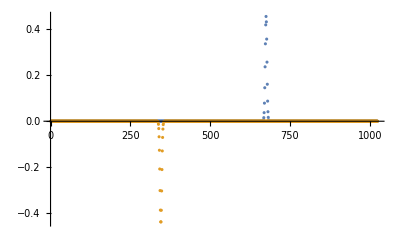

```mathematica
ListPlot[{wfcH267red⟦2,1⟧,wfcH267ox⟦2,1⟧},PlotRange->All]
```

```mathematica
pestable237ox=Table[pes237⟦i⟧⟦3⟧,{i,1,1024}];
pestable237ox=pestable237ox-Min[pestable237ox];wfcH237ox=GenGridSolverND[pestable237ox,1.25,10,M->mH];
pestable242ox=Table[pes242⟦i⟧⟦3⟧,{i,1,1024}];
pestable242ox=pestable242ox-Min[pestable242ox];
wfcH242ox=GenGridSolverND[pestable242ox,1.25,10,M->mH];
pestable247ox=Table[pes247⟦i⟧⟦3⟧,{i,1,1024}];
pestable247ox=pestable247ox-Min[pestable247ox];wfcH247ox=GenGridSolverND[pestable247ox,1.25,10,M->mH];
pestable252ox=Table[pes252⟦i⟧⟦3⟧,{i,1,1024}];
pestable252ox=pestable252ox-Min[pestable252ox];
wfcH252ox=GenGridSolverND[pestable252ox,1.25,10,M->mH];
pestable257ox=Table[pes257⟦i⟧⟦3⟧,{i,1,1024}];
pestable257ox=pestable257ox-Min[pestable257ox];wfcH257ox=GenGridSolverND[pestable257ox,1.25,10,M->mH];
pestable262ox=Table[pes262⟦i⟧⟦3⟧,{i,1,1024}];
pestable262ox=pestable262ox-Min[pestable262ox];
wfcH262ox=GenGridSolverND[pestable262ox,1.25,10,M->mH];
pestable267ox=Table[pes267⟦i⟧⟦3⟧,{i,1,1024}];
pestable267ox=pestable267ox-Min[pestable267ox];wfcH267ox=GenGridSolverND[pestable267ox,1.25,10,M->mH];
pestable272ox=Table[pes272⟦i⟧⟦3⟧,{i,1,1024}];
pestable272ox=pestable272ox-Min[pestable272ox];
wfcH272ox=GenGridSolverND[pestable272ox,1.25,10,M->mH];
pestable277ox=Table[pes277⟦i⟧⟦3⟧,{i,1,1024}];
pestable277ox=pestable277ox-Min[pestable277ox];wfcH277ox=GenGridSolverND[pestable277ox,1.25,10,M->mH];
pestable282ox=Table[pes282⟦i⟧⟦3⟧,{i,1,1024}];
pestable282ox=pestable282ox-Min[pestable282ox];
wfcH282ox=GenGridSolverND[pestable282ox,1.25,10,M->mH];
pestable287ox=Table[pes287⟦i⟧⟦3⟧,{i,1,1024}];
pestable287ox=pestable287ox-Min[pestable287ox];wfcH287ox=GenGridSolverND[pestable287ox,1.25,10,M->mH];
```

Calculate vibrational states for all PT profiles (take a bit of time):
(Note that the package settings assume that the executable fgh_bspline.bin is found in /usr/local/bspline/bin)

```mathematica
FGHWavefunctions[file_,nGridPoints_,nStates_,OptionsPattern[{M->MassH}]]:=Module[{mass,massString,filename,nG,nS,error,command,reactantEnergies,productEnergies,reactantPotential,productPotential,reactantWavefunctions,productWavefunctions,overlapMatrix,alphaMatrix},filename=StringSplit[file,"."][[1]];
nG=nGridPoints;
(*Check if nStates<nGridPoints,otherwise set nStates to default value of 10*)If[nStates<nGridPoints,nS=nStates,nS=10];
mass=OptionValue[M]*Dalton;
massString=ToString[FortranForm[mass]];
(*run external executable to generate all the data*)command=" /usr/local/bspline/bin/fgh_bspline.bin "<>file<>" "<>ToString[nG]<>" "<>massString<>" "<>ToString[nS];
error=Run[command];
If[error≠0,Message[FGHWavefunctions::noexec];Abort[]];
(*Read energies from disk*)reactantEnergies=ReadList[filename<>"_reactant_en.dat",Real];
productEnergies=ReadList[filename<>"_product_en.dat",Real];
(*Read splined potentials from disk*)reactantPotential=Part[ReadList[filename<>"_bspline.dat",{Real,Real,Real}],All,{1,2}];
productPotential=Part[ReadList[filename<>"_bspline.dat",{Real,Real,Real}],All,{1,3}];
(*Read wavefunctions from disk*)reactantWavefunctions={};
productWavefunctions={};
Do[reactantWavefunctions=Append[reactantWavefunctions,Part[ReadList[filename<>"_reactant_wf.dat",Table[Real,{k,1,1+nS}]],All,1+i]],{i,1,nS}];
Do[productWavefunctions=Append[productWavefunctions,Part[ReadList[filename<>"_product_wf.dat",Table[Real,{k,1,1+nS}]],All,1+i]],{i,1,nS}];
(*Read overlap matrix from disk*)overlapMatrix=ReadList[filename<>"_overlaps.dat",Table[Real,{k,1,nS}]];
(*Read alpha matrix from disk*)alphaMatrix=ReadList[filename<>"_alphas.dat",Table[Real,{k,1,nS}]];
(*clean the data files in the current directoryDeleteFile[FileNames[filename<>"_*.dat"]];*)
(*Now gather all the results in one nested list*){{reactantEnergies,reactantPotential,reactantWavefunctions},{productEnergies,productPotential,productWavefunctions},overlapMatrix,alphaMatrix}];
```

```mathematica
Directory[]
```

/Users/Zach/Box Sync/Work/Triads_PCET/Mathematica

```mathematica
FGHWavefunctions["06_d237_pes.dat",64,3]
```

ReadList::readf: Real  is not a valid format specification.

Part::partd: Part specification ReadList[06_d237_pes_reactant_wf.dat,{Real ,Real ,Real ,Real }]⟦All,2⟧ is longer than depth of object.

ReadList::readf: Real  is not a valid format specification.

Part::partd: Part specification ReadList[06_d237_pes_reactant_wf.dat,{Real ,Real ,Real ,Real }]⟦All,3⟧ is longer than depth of object.

ReadList::readf: Real  is not a valid format specification.

General::stop: Further output of ReadList::readf will be suppressed during this calculation.

Part::partd: Part specification ReadList[06_d237_pes_reactant_wf.dat,{Real ,Real ,Real ,Real }]⟦All,4⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{{{2.47014,6.21865,10.5526},{{-1.25,451.302},{-1.21032,451.302},{-1.17063,451.302},{-1.13095,451.302},{-1.09127,451.302},{-1.05159,451.302},{-1.0119,451.302},{-0.972222,424.518},{-0.93254,386.115},{-0.892857,345.523},{-0.853175,302.941},{-0.813492,260.965},{-0.77381,221.489},{-0.734127,185.116},{-0.694444,152.272},{-0.654762,123.221},{-0.615079,98.1382},{-0.575397,76.8854},{-0.535714,59.2223},{-0.496032,44.8348},{-0.456349,33.369},{-0.416667,24.4533},{-0.376984,17.7007},{-0.337302,12.7407},{-0.297619,9.22746},{-0.257937,6.83427},{-0.218254,5.27721},{-0.178571,4.2916},{-0.138889,3.66814},{-0.0992063,3.22004},{-0.0595238,2.82022},{-0.0198413,2.37327},{0.0198413,1.8427},{0.0595238,1.23932},{0.0992063,0.630016},{0.138889,0.152527},{0.178571,0.},{0.218254,0.474856},{0.257937,1.93629},{0.297619,4.90313},{0.337302,9.9732},{0.376984,18.0235},{0.416667,30.069},{0.456349,47.4242},{0.496032,71.6378},{0.535714,105.046},{0.575397,150.884},{0.615079,212.56},{0.654762,293.714},{0.694444,400.446},{0.734127,546.868},{0.77381,746.714},{0.813492,1001.85},{0.853175,1316.39},{0.892857,1766.23},{0.93254,2465.01},{0.972222,3366.86},{1.0119,4007.14},{1.05159,4007.13},{1.09127,4007.13},{1.13095,4007.13},{1.17063,4007.13},{1.21032,4007.13},{1.25,4007.13}},{ReadList[06_d237_pes_reactant_wf.dat,{Real ,Real ,Real ,Real }]⟦All,2⟧,ReadList[06_d237_pes_reactant_wf.dat,{Real ,Real ,Real ,Real }]⟦All,3⟧,ReadList[06_d237_pes_reactant_wf.dat,{Real ,Real ,Real ,Real }]⟦All,4⟧}},{{2.54003,6.75127,11.0087},{{-1.25,439.471},{-1.21032,439.471},{-1.17063,439.471},{-1.13095,439.471},{-1.09127,439.471},{-1.05159,439.471},{-1.0119,439.471},{-0.972222,412.775},{-0.93254,374.496},{-0.892857,334.022},{-0.853175,291.552},{-0.813492,249.688},{-0.77381,210.332},{-0.734127,174.092},{-0.694444,141.398},{-0.654762,112.521},{-0.615079,87.6394},{-0.575397,66.6241},{-0.535714,49.2419},{-0.496032,35.1869},{-0.456349,24.1137},{-0.416667,15.6579},{-0.376984,9.43957},{-0.337302,5.09452},{-0.297619,2.28287},{-0.257937,0.682504},{-0.218254,0.0101959},{-0.178571,0.},{-0.138889,0.435101},{-0.0992063,1.11879},{-0.0595238,1.90833},{-0.0198413,2.68974},{0.0198413,3.4054},{0.0595238,4.04296},{0.0992063,4.64752},{0.138889,5.33679},{0.178571,6.28707},{0.218254,7.79044},{0.257937,10.1986},{0.297619,14.0302},{0.337302,19.8853},{0.376984,28.6464},{0.416667,41.3357},{0.456349,59.2757},{0.496032,84.0232},{0.535714,117.923},{0.575397,164.218},{0.615079,226.322},{0.654762,307.883},{0.694444,415.009},{0.734127,561.818},{0.77381,762.052},{0.813492,1017.58},{0.853175,1332.52},{0.892857,1782.8},{0.93254,2482.07},{0.972222,3384.46},{1.0119,4025.13},{1.05159,4025.13},{1.09127,4025.13},{1.13095,4025.13},{1.17063,4025.13},{1.21032,4025.13},{1.25,4025.13}},{ReadList[06_d237_pes_product_wf.dat,{Real ,Real ,Real ,Real }]⟦All,2⟧,ReadList[06_d237_pes_product_wf.dat,{Real ,Real ,Real ,Real }]⟦All,3⟧,ReadList[06_d237_pes_product_wf.dat,{Real ,Real ,Real ,Real }]⟦All,4⟧}},ReadList[06_d237_pes_overlaps.dat,{Real ,Real ,Real }],ReadList[06_d237_pes_alphas.dat,{Real ,Real ,Real }]}

```mathematica
ReadList["06_d237_pes_reactant_wf.dat",{Number ,Number ,Number ,Number }]⟦All,4⟧
```

{3.69887×10^-16,8.34248×10^-16,1.27749×10^-15,2.0482×10^-15,2.74425×10^-15,3.23442×10^-15,3.61419×10^-15,3.89628×10^-15,4.03147×10^-15,4.18487×10^-15,4.14416×10^-15,3.78328×10^-15,3.14501×10^-15,2.44502×10^-15,1.71531×10^-15,1.4186×10^-15,1.01389×10^-15,1.00688×10^-15,1.01689×10^-15,7.3796×10^-16,7.08336×10^-16,5.48454×10^-16,1.15847×10^-15,1.81604×10^-15,2.00638×10^-15,1.68759×10^-15,1.53034×10^-15,1.26611×10^-15,1.28204×10^-15,1.60802×10^-15,1.72918×10^-15,1.57108×10^-15,1.36535×10^-15,7.28072×10^-16,7.73615×10^-16,7.80012×10^-16,6.15696×10^-16,5.6328×10^-16,4.26483×10^-16,5.31351×10^-17,1.69832×10^-16,1.14316×10^-16,8.07313×10^-17,8.40305×10^-17,5.7161×10^-16,7.71134×10^-16,1.15811×10^-15,1.22874×10^-15,1.06043×10^-15,7.29149×10^-16,6.51601×10^-16,7.37517×10^-16,8.51041×10^-16,8.15182×10^-16,6.0611×10^-16,5.68225×10^-16,4.27182×10^-16,4.44249×10^-16,1.16201×10^-16,-1.65137×10^-16,-4.95944×10^-16,-1.11167×10^-15,-1.59977×10^-15,-1.88422×10^-15,-1.77911×10^-15,-1.26228×10^-15,-5.67021×10^-16,1.24905×10^-16,8.00288×10^-16,1.43504×10^-15,2.35087×10^-15,3.15808×10^-15,3.93461×10^-15,4.51174×10^-15,5.04877×10^-15,5.02731×10^-15,4.90849×10^-15,4.5837×10^-15,4.82146×10^-15,4.86467×10^-15,4.80954×10^-15,4.46444×10^-15,4.32428×10^-15,4.04352×10^-15,3.86122×10^-15,3.87689×10^-15,4.02858×10^-15,4.28059×10^-15,4.40864×10^-15,4.59756×10^-15,4.30265×10^-15,4.60322×10^-15,4.71614×10^-15,4.71354×10^-15,4.52844×10^-15,3.76542×10^-15,3.22391×10^-15,2.67541×10^-15,2.28832×10^-15,1.63855×10^-15,1.30385×10^-15,8.52271×10^-16,3.988×10^-16,2.27253×10^-16,-8.71724×10^-17,2.7031×10^-16,7.26283×10^-16,1.44574×10^-15,2.12342×10^-15,2.55744×10^-15,2.84763×10^-15,3.50757×10^-15,4.21435×10^-15,4.74815×10^-15,4.78894×10^-15,4.22211×10^-15,3.09604×10^-15,1.92534×10^-15,1.04471×10^-15,-5.07623×10^-17,-1.22757×10^-15,-3.09328×10^-15,-4.37827×10^-15,-5.58063×10^-15,-6.70214×10^-15,-7.58962×10^-15,-9.03483×10^-15,-1.02454×10^-14,-1.18101×10^-14,-1.37258×10^-14,-1.55889×10^-14,-1.83416×10^-14,-2.19421×10^-14,-2.69478×10^-14,-3.26067×10^-14,-3.96408×10^-14,-4.80313×10^-14,-5.78238×10^-14,-6.95891×10^-14,-8.42477×10^-14,-1.01721×10^-13,-1.2339×10^-13,-1.50279×10^-13,-1.83364×10^-13,-2.24422×10^-13,-2.75356×10^-13,-3.38644×10^-13,-4.16271×10^-13,-5.12079×10^-13,-6.28563×10^-13,-7.70699×10^-13,-9.43399×10^-13,-1.15353×10^-12,-1.40982×10^-12,-1.72253×10^-12,-2.10337×10^-12,-2.56696×10^-12,-3.12956×10^-12,-3.81176×10^-12,-4.63896×10^-12,-5.64129×10^-12,-6.85501×10^-12,-8.32265×10^-12,-1.00953×10^-11,-1.22356×10^-11,-1.48168×10^-11,-1.79279×10^-11,-2.1673×10^-11,-2.61777×10^-11,-3.15917×10^-11,-3.80925×10^-11,-4.58918×10^-11,-5.52404×10^-11,-6.64359×10^-11,-7.98314×10^-11,-9.5845×10^-11,-1.14971×10^-10,-1.37795×10^-10,-1.65005×10^-10,-1.97416×10^-10,-2.35988×10^-10,-2.8185×10^-10,-3.36331×10^-10,-4.0099×10^-10,-4.77661×10^-10,-5.68491×10^-10,-6.76×10^-10,-8.03134×10^-10,-9.53338×10^-10,-1.13064×10^-9,-1.33973×10^-9,-1.58609×10^-9,-1.8761×10^-9,-2.21718×10^-9,-2.61795×10^-9,-3.08843×10^-9,-3.64025×10^-9,-4.28687×10^-9,-5.04388×10^-9,-5.92932×10^-9,-6.96403×10^-9,-8.17206×10^-9,-9.58115×10^-9,-1.12233×10^-8,-1.31352×10^-8,-1.53591×10^-8,-1.79438×10^-8,-2.09447×10^-8,-2.4426×10^-8,-2.84606×10^-8,-3.31322×10^-8,-3.85366×10^-8,-4.47828×10^-8,-5.19953×10^-8,-6.03161×10^-8,-6.99066×10^-8,-8.09504×10^-8,-9.36561×10^-8,-1.0826×10^-7,-1.25031×10^-7,-1.44273×10^-7,-1.6633×10^-7,-1.91589×10^-7,-2.2049×10^-7,-2.53527×10^-7,-2.91259×10^-7,-3.34312×10^-7,-3.83392×10^-7,-4.39292×10^-7,-5.02901×10^-7,-5.75217×10^-7,-6.57357×10^-7,-7.50571×10^-7,-8.56254×10^-7,-9.75967×10^-7,-1.11145×10^-6,-1.26464×10^-6,-1.43769×10^-6,-1.63301×10^-6,-1.85325×10^-6,-2.10139×10^-6,-2.38069×10^-6,-2.69478×10^-6,-3.0477×10^-6,-3.44387×10^-6,-3.88821×10^-6,-4.38612×10^-6,-4.94356×10^-6,-5.56711×10^-6,-6.26397×10^-6,-7.04208×10^-6,-7.91015×10^-6,-8.87771×10^-6,-9.95521×10^-6,-0.0000111541,-0.0000124869,-0.0000139672,-0.00001561,-0.0000174314,-0.0000194492,-0.0000216825,-0.0000241523,-0.0000268812,-0.0000298937,-0.0000332165,-0.0000368784,-0.0000409105,-0.0000453464,-0.0000502224,-0.0000555776,-0.0000614539,-0.0000678967,-0.0000749546,-0.0000826796,-0.0000911277,-0.000100359,-0.000110437,-0.00012143,-0.000133412,-0.000146461,-0.000160659,-0.000176095,-0.000192863,-0.000211063,-0.0002308,-0.000252187,-0.000275342,-0.000300391,-0.000327467,-0.00035671,-0.000388268,-0.000422294,-0.000458954,-0.000498419,-0.000540868,-0.000586491,-0.000635486,-0.000688058,-0.000744424,-0.00080481,-0.00086945,-0.000938588,-0.00101248,-0.00109139,-0.00117558,-0.00126536,-0.00136099,-0.0014628,-0.00157109,-0.00168619,-0.00180842,-0.00193813,-0.00207566,-0.00222138,-0.00237566,-0.00253886,-0.00271137,-0.00289358,-0.00308589,-0.00328869,-0.00350241,-0.00372744,-0.00396421,-0.00421315,-0.00447466,-0.00474919,-0.00503715,-0.00533898,-0.00565509,-0.00598592,-0.00633189,-0.0066934,-0.00707088,-0.00746474,-0.00787536,-0.00830313,-0.00874845,-0.00921166,-0.00969314,-0.0101932,-0.0107122,-0.0112504,-0.0118082,-0.0123857,-0.0129832,-0.0136011,-0.0142393,-0.0148982,-0.0155779,-0.0162784,-0.017,-0.0177426,-0.0185062,-0.0192909,-0.0200966,-0.0209232,-0.0217706,-0.0226386,-0.0235271,-0.0244357,-0.0253643,-0.0263125,-0.0272798,-0.028266,-0.0292705,-0.0302929,-0.0313325,-0.0323889,-0.0334613,-0.034549,-0.0356515,-0.0367678,-0.0378971,-0.0390386,-0.0401913,-0.0413544,-0.0425267,-0.0437074,-0.0448951,-0.0460889,-0.0472876,-0.04849,-0.0496948,-0.0509007,-0.0521065,-0.0533107,-0.0545121,-0.0557092,-0.0569005,-0.0580847,-0.0592601,-0.0604254,-0.061579,-0.0627194,-0.0638449,-0.0649541,-0.0660453,-0.0671171,-0.0681677,-0.0691956,-0.0701992,-0.071177,-0.0721273,-0.0730486,-0.0739393,-0.0747979,-0.0756229,-0.0764127,-0.0771659,-0.077881,-0.0785565,-0.0791912,-0.0797836,-0.0803323,-0.0808362,-0.0812938,-0.0817041,-0.0820658,-0.0823778,-0.082639,-0.0828485,-0.0830052,-0.0831082,-0.0831566,-0.0831496,-0.0830865,-0.0829666,-0.0827892,-0.0825538,-0.0822599,-0.081907,-0.0814947,-0.0810228,-0.0804909,-0.079899,-0.0792468,-0.0785345,-0.077762,-0.0769293,-0.0760368,-0.0750846,-0.0740731,-0.0730025,-0.0718735,-0.0706865,-0.0694421,-0.068141,-0.0667838,-0.0653715,-0.0639048,-0.0623848,-0.0608123,-0.0591885,-0.0575145,-0.0557914,-0.0540206,-0.0522033,-0.0503408,-0.0484347,-0.0464863,-0.0444973,-0.0424691,-0.0404035,-0.038302,-0.0361665,-0.0339987,-0.0318005,-0.0295736,-0.0273201,-0.0250418,-0.0227407,-0.0204189,-0.0180784,-0.0157213,-0.0133498,-0.0109658,-0.00857172,-0.00616964,-0.0037618,-0.00135044,0.00106219,0.00347382,0.00588216,0.00828491,0.0106798,0.0130644,0.0154366,0.0177939,0.020134,0.0224547,0.0247535,0.0270283,0.0292766,0.0314962,0.0336848,0.0358402,0.03796,0.0400422,0.0420843,0.0440844,0.0460401,0.0479495,0.0498103,0.0516205,0.0533781,0.0550811,0.0567275,0.0583154,0.0598431,0.0613085,0.0627101,0.064046,0.0653146,0.0665143,0.0676437,0.0687011,0.0696852,0.0705946,0.0714281,0.0721845,0.0728626,0.0734613,0.0739798,0.0744171,0.0747724,0.0750449,0.0752341,0.0753393,0.0753602,0.0752963,0.0751473,0.0749131,0.0745935,0.0741887,0.0736986,0.0731236,0.0724639,0.0717198,0.0708921,0.0699812,0.0689879,0.0679131,0.0667576,0.0655226,0.0642092,0.0628186,0.0613523,0.0598117,0.0581984,0.0565141,0.0547606,0.0529398,0.0510537,0.0491044,0.0470941,0.0450252,0.0428999,0.0407207,0.0384904,0.0362114,0.0338865,0.0315186,0.0291105,0.0266653,0.0241859,0.0216754,0.019137,0.0165739,0.0139893,0.0113866,0.00876915,0.00614024,0.00350332,0.000861827,-0.0017808,-0.00442109,-0.00705557,-0.00968078,-0.0122933,-0.0148896,-0.0174662,-0.0200199,-0.0225472,-0.0250447,-0.0275093,-0.0299376,-0.0323265,-0.0346729,-0.0369737,-0.039226,-0.041427,-0.0435737,-0.0456636,-0.047694,-0.0496625,-0.0515668,-0.0534044,-0.0551735,-0.0568718,-0.0584977,-0.0600493,-0.0615251,-0.0629235,-0.0642434,-0.0654835,-0.0666429,-0.0677206,-0.068716,-0.0696286,-0.0704579,-0.0712038,-0.0718661,-0.0724449,-0.0729405,-0.0733533,-0.0736838,-0.0739327,-0.0741009,-0.0741894,-0.0741993,-0.0741318,-0.0739885,-0.0737708,-0.0734804,-0.073119,-0.0726887,-0.0721914,-0.0716292,-0.0710043,-0.070319,-0.0695757,-0.0687769,-0.067925,-0.0670227,-0.0660726,-0.0650773,-0.0640395,-0.0629621,-0.0618477,-0.0606992,-0.0595192,-0.0583107,-0.0570763,-0.0558188,-0.054541,-0.0532456,-0.0519353,-0.0506126,-0.0492802,-0.0479406,-0.0465963,-0.0452498,-0.0439033,-0.0425592,-0.0412196,-0.0398867,-0.0385626,-0.0372491,-0.0359481,-0.0346615,-0.0333908,-0.0321376,-0.0309035,-0.0296897,-0.0284977,-0.0273284,-0.0261831,-0.0250626,-0.0239679,-0.0228997,-0.0218587,-0.0208455,-0.0198606,-0.0189043,-0.017977,-0.0170789,-0.0162101,-0.0153707,-0.0145606,-0.0137799,-0.0130282,-0.0123055,-0.0116114,-0.0109455,-0.0103075,-0.00969703,-0.00911348,-0.00855635,-0.0080251,-0.00751911,-0.00703775,-0.00658039,-0.00614633,-0.00573489,-0.00534535,-0.00497698,-0.00462906,-0.00430085,-0.0039916,-0.00370057,-0.00342702,-0.0031702,-0.0029294,-0.00270389,-0.00249295,-0.00229589,-0.00211201,-0.00194066,-0.00178117,-0.00163291,-0.00149525,-0.00136761,-0.00124939,-0.00114005,-0.00103903,-0.000945837,-0.000859962,-0.000780934,-0.000708301,-0.000641633,-0.000580518,-0.000524568,-0.000473414,-0.000426706,-0.000384116,-0.000345331,-0.00031006,-0.000278028,-0.000248977,-0.000222666,-0.00019887,-0.000177378,-0.000157994,-0.000140536,-0.000124836,-0.000110736,-0.0000980914,-0.0000867687,-0.0000766444,-0.0000676049,-0.0000595459,-0.0000523718,-0.000045995,-0.0000403354,-0.00003532,-0.0000308822,-0.0000269615,-0.0000235032,-0.0000204573,-0.0000177789,-0.0000154274,-0.0000133662,-0.0000115623,-9.98617×10^-6,-8.61123×10^-6,-7.41377×10^-6,-6.3726×10^-6,-5.46882×10^-6,-4.68558×10^-6,-4.00796×10^-6,-3.4227×10^-6,-2.91805×10^-6,-2.48367×10^-6,-2.1104×10^-6,-1.79021×10^-6,-1.51601×10^-6,-1.28162×10^-6,-1.0816×10^-6,-9.11224×10^-7,-7.66346×10^-7,-6.43375×10^-7,-5.39184×10^-7,-4.51065×10^-7,-3.76674×10^-7,-3.13988×10^-7,-2.61261×10^-7,-2.16994×10^-7,-1.79898×10^-7,-1.4887×10^-7,-1.22965×10^-7,-1.01379×10^-7,-8.34256×10^-8,-6.85218×10^-8,-5.61733×10^-8,-4.59618×10^-8,-3.75339×10^-8,-3.05915×10^-8,-2.48841×10^-8,-2.02014×10^-8,-1.63669×10^-8,-1.32335×10^-8,-1.06781×10^-8,-8.59839×10^-9,-6.90932×10^-9,-5.54038×10^-9,-4.43323×10^-9,-3.53972×10^-9,-2.82017×10^-9,-2.24198×10^-9,-1.77838×10^-9,-1.4075×10^-9,-1.11146×10^-9,-8.75678×10^-10,-6.88328×10^-10,-5.39804×10^-10,-4.22332×10^-10,-3.29639×10^-10,-2.56673×10^-10,-1.99374×10^-10,-1.54487×10^-10,-1.19411×10^-10,-9.20677×10^-11,-7.08068×10^-11,-5.43167×10^-11,-4.15601×10^-11,-3.1717×10^-11,-2.41414×10^-11,-1.83268×10^-11,-1.38754×10^-11,-1.04767×10^-11,-7.8893×10^-12,-5.92484×10^-12,-4.43698×10^-12,-3.31342×10^-12,-2.46752×10^-12,-1.83258×10^-12,-1.35754×10^-12,-1.00234×10^-12,-7.38062×10^-13,-5.42355×10^-13,-3.96829×10^-13,-2.89839×10^-13,-2.11417×10^-13,-1.53783×10^-13,-1.11282×10^-13,-8.01981×10^-14,-5.78571×10^-14,-4.19637×10^-14,-3.07624×10^-14,-2.21156×10^-14,-1.53311×10^-14,-1.07976×10^-14,-8.07398×10^-15,-6.16049×10^-15,-4.80595×10^-15,-3.66362×10^-15,-2.42149×10^-15,-1.59433×10^-15,-1.53603×10^-15,-1.01959×10^-15,-1.84351×10^-16,2.86714×10^-16,2.383×10^-16,1.85644×10^-16,-1.80065×10^-16,-4.0362×10^-16,-1.90634×10^-17,6.41214×10^-16,5.61908×10^-16,5.22585×10^-16,5.70902×10^-16,4.58856×10^-16,3.96051×10^-16,1.69258×10^-16,-5.9477×10^-17,-1.95298×10^-16,-3.31906×10^-16,-6.0309×10^-16,-4.74828×10^-16,-2.83482×10^-16,9.32797×10^-17,3.71554×10^-16,2.39118×10^-16,7.40088×10^-17,-7.02075×10^-17,4.95313×10^-17,2.00299×10^-16,1.63326×10^-16,1.15764×10^-17,-2.39763×10^-16,-5.39162×10^-16,-3.96366×10^-16,-2.71151×10^-16,-6.29207×10^-17,5.06007×10^-19,1.25178×10^-16,1.35995×10^-17,1.39746×10^-17,1.07306×10^-16,-1.70549×10^-17,-1.48929×10^-16,-1.35232×10^-16,6.46272×10^-17,3.18438×10^-16,5.39434×10^-16,3.02498×10^-16,-6.67676×10^-17,-1.71074×10^-16,-4.32357×10^-16,-1.42184×10^-16,1.42969×10^-16,4.30597×10^-16,5.66345×10^-16,3.24014×10^-16,3.07253×10^-16,5.93328×10^-17,-1.66116×10^-17,2.01157×10^-16,3.14855×10^-16,2.23993×10^-16,7.41371×10^-17,1.50176×10^-16,1.0472×10^-17,4.15164×10^-17,5.48389×10^-18,-1.0785×10^-16,-2.8734×10^-16,5.98472×10^-17,2.26311×10^-16,2.57156×10^-16,5.2872×10^-17,2.06344×10^-16,1.00824×10^-16,-2.82713×10^-17,-4.63594×10^-17,-8.58403×10^-17,1.81005×10^-16,4.10361×10^-16,6.00562×10^-16,6.71185×10^-16,2.02102×10^-16,-6.61902×10^-17,-2.88349×10^-16,-2.08195×10^-16,-6.7298×10^-17,2.65138×10^-17,1.52854×10^-16,1.44255×10^-16,1.41067×10^-16,-9.25913×10^-17,8.9509×10^-17,5.39384×10^-16,5.57056×10^-16,4.33225×10^-16,1.03172×10^-16,8.60103×10^-18,-2.626×10^-16,-4.6149×10^-16,-2.15668×10^-16,-3.25372×10^-16,-2.91555×10^-16,-3.42547×10^-16,7.54224×10^-17,8.32458×10^-17,2.25329×10^-16,3.09258×10^-16,2.32912×10^-16,3.67436×10^-16,3.23224×10^-16,1.34787×10^-16,-4.15406×10^-17,-7.59034×10^-17,-1.81623×10^-16,5.72254×10^-17,9.94435×10^-17,3.80878×10^-16,2.33766×10^-16,9.16189×10^-17,2.50324×10^-17,1.09227×10^-16,9.18818×10^-17,1.14577×10^-16,7.76559×10^-17,1.18766×10^-16,7.45847×10^-17,-1.05426×10^-17,-1.84005×10^-16,6.3291×10^-17,3.00125×10^-17,9.21118×10^-17,-2.14396×10^-16,-3.04898×10^-16,1.31088×10^-17,3.02801×10^-16,7.08155×10^-16,6.7658×10^-16,4.46972×10^-16,2.92578×10^-16,-9.6375×10^-17,-3.47452×10^-16,-7.38443×10^-17,7.41863×10^-17,-9.54348×10^-19,8.58351×10^-18,5.34865×10^-17,4.54321×10^-17,1.01188×10^-16,-9.72482×10^-18,2.70722×10^-17,-1.94745×10^-16,-4.04455×10^-16,-6.7867×10^-16,-5.53741×10^-16,-3.42881×10^-16,-1.97966×10^-16,5.94817×10^-17,2.2397×10^-16,2.98966×10^-16,3.22182×10^-16,1.51738×10^-16,-5.63276×10^-17,-2.01863×10^-16,-1.82818×10^-16,2.94356×10^-17,1.0395×10^-16,3.56874×10^-16,5.30074×10^-16,4.63178×10^-16,1.32271×10^-18,-1.23346×10^-16,-1.67397×10^-16,-1.82839×10^-16,2.86276×10^-17,2.05603×10^-16}

```mathematica
waveH237=FGHWavefunctions["06_d237_pes.dat",1024,8]
waveH242=FGHWavefunctions["06_d242_pes.dat",1024,8];
waveH247=FGHWavefunctions["06_d247_pes.dat",1024,8];
waveH252=FGHWavefunctions["06_d252_pes.dat",1024,8];
waveH257=FGHWavefunctions["06_d257_pes.dat",1024,8];
waveH262=FGHWavefunctions["06_d262_pes.dat",1024,8];
waveH267=FGHWavefunctions["06_d267_pes.dat",1024,8];
waveH272=FGHWavefunctions["06_d272_pes.dat",1024,8];
waveH277=FGHWavefunctions["06_d277_pes.dat",1024,8];
waveH282=FGHWavefunctions["06_d282_pes.dat",1024,8];
waveH287=FGHWavefunctions["06_d287_pes.dat",1024,8];
```

FGHWavefunctions[06_d237_pes.dat,1024,8]

```mathematica
waveD237=FGHWavefunctions["06_d237_pes.dat",1024,8,M->MassD];
waveD242=FGHWavefunctions["06_d242_pes.dat",1024,8,M->MassD];
waveD247=FGHWavefunctions["06_d247_pes.dat",1024,8,M->MassD];
waveD252=FGHWavefunctions["06_d252_pes.dat",1024,8,M->MassD];
waveD257=FGHWavefunctions["06_d257_pes.dat",1024,8,M->MassD];
waveD262=FGHWavefunctions["06_d262_pes.dat",1024,8,M->MassD];
waveD267=FGHWavefunctions["06_d267_pes.dat",1024,8,M->MassD];
waveD272=FGHWavefunctions["06_d272_pes.dat",1024,8,M->MassD];
waveD277=FGHWavefunctions["06_d277_pes.dat",1024,8,M->MassD];
waveD282=FGHWavefunctions["06_d282_pes.dat",1024,8,M->MassD];
waveD287=FGHWavefunctions["06_d287_pes.dat",1024,8,M->MassD];
```

Check (visualize) the wavefunctions:

```mathematica
GraphicsRow[
{ListLinePlot[{waveH257⟦1,3,1⟧,waveH257⟦2,3,1⟧},PlotRange->All]},
ImageSize->Medium
]
```

Part::partd: Part specification FGHWavefunctions[06_d257_pes.dat,1024,8]⟦1,3,1⟧ is longer than depth of object.

Part::partd: Part specification FGHWavefunctions[06_d257_pes.dat,1024,8]⟦2,3,1⟧ is longer than depth of object.

Part::partd: Part specification FGHWavefunctions[06_d257_pes.dat,1024.,8.]⟦1,3,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

More elaborate plots for checking that everything makes sense:

```mathematica
wavelist=waveH257;
ListLinePlot[{Table[{wavelist[[1,2]][[i,1]],wavelist[[1,2]][[i,2]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[1]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[1]]+50*wavelist[[1,3,1]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[2]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[2]]+50*wavelist[[1,3,2]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[3]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[3]]+50*wavelist[[1,3,3]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[4]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[4]]+50*wavelist[[1,3,4]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[5]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[5]]+50*wavelist[[1,3,5]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[6]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[6]]+50*wavelist[[1,3,6]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}]},PlotRange->{0,30},ImageSize->Large,BaseStyle->{FontSize->16},Axes->False,Frame->True,FrameLabel->{"Proton coordinate [Å]","Energy [kcal/mol]"},PlotStyle->{{Black,Thick},Red,Red,Green,Green,Blue,Blue,Magenta,Magenta,Cyan,Cyan,Orange,Orange}]
```

Part::partd: Part specification FGHWavefunctions[06_d257_pes.dat,1024,8]⟦1,3,1⟧ is longer than depth of object.

Part::partd: Part specification FGHWavefunctions[06_d257_pes.dat,1024,8]⟦1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 4 of FGHWavefunctions[06_d257_pes.dat,1024,8]⟦1,2⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

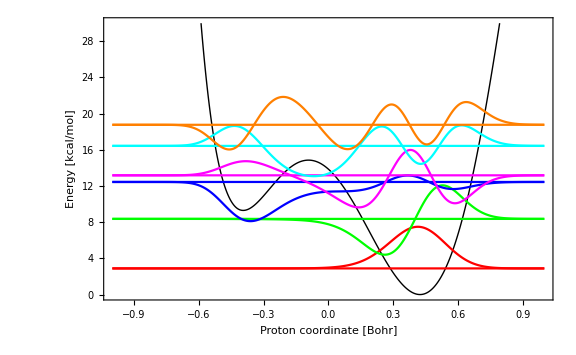

```mathematica
wavelist=waveH262;
ListLinePlot[{Table[{wavelist[[2,2]][[i,1]],wavelist[[2,2]][[i,2]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[1]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[1]]+50*wavelist[[2,3,1]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[2]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[2]]+50*wavelist[[2,3,2]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[3]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[3]]+50*wavelist[[2,3,3]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[4]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[4]]+50*wavelist[[2,3,4]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[5]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[5]]+50*wavelist[[2,3,5]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[6]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[6]]+50*wavelist[[2,3,6]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}]},PlotRange->{0,30},ImageSize->Large,BaseStyle->{FontSize->16},Axes->False,Frame->True,FrameLabel->{"Proton coordinate [Bohr]","Energy [kcal/mol]"},PlotStyle->{{Black,Thick},Red,Red,Green,Green,Blue,Blue,Magenta,Magenta,Cyan,Cyan,Orange,Orange}]
```

## Functions for anodic (ka) and cathodic (kc) total rate constants - Proton

Anodic rate constant k_a(η):
(mumax and numax are the upper limits for the vibrational quantum numbers for the reactant and product vibrational states)

```mathematica
kaHEPTtotal[η_,mumax_,numax_,OptionsPattern[{Output->False}]]:=Module[
{output,kaH237,kaH242,kaH247,kaH252,kaH257,kaH262,kaH267,kaH272,kaH277,kaH282,kaH287,listkAH,kaHR,kaHtotal,kaH,kaHmax},

output=OptionValue[Output];

kaH237=AnodicRateConstantFGHBen[waveH237,Vel,η,λs,mumax,numax,T];
kaH242=AnodicRateConstantFGHBen[waveH242,Vel,η,λs,mumax,numax,T];
kaH247=AnodicRateConstantFGHBen[waveH247,Vel,η,λs,mumax,numax,T];
kaH252=AnodicRateConstantFGHBen[waveH252,Vel,η,λs,mumax,numax,T];
kaH257=AnodicRateConstantFGHBen[waveH257,Vel,η,λs,mumax,numax,T];
kaH262=AnodicRateConstantFGHBen[waveH262,Vel,η,λs,mumax,numax,T];
kaH267=AnodicRateConstantFGHBen[waveH267,Vel,η,λs,mumax,numax,T];
kaH272=AnodicRateConstantFGHBen[waveH272,Vel,η,λs,mumax,numax,T];
kaH277=AnodicRateConstantFGHBen[waveH277,Vel,η,λs,mumax,numax,T];
kaH282=AnodicRateConstantFGHBen[waveH282,Vel,η,λs,mumax,numax,T];
kaH287=AnodicRateConstantFGHBen[waveH287,Vel,η,λs,mumax,numax,T];

listkAH={{R237,kaH237},{R242,kaH242},{R247,kaH247},{R252,kaH252},{R257,kaH257},{R262,kaH262},{R267,kaH267},{R272,kaH272},{R277,kaH277},{R282,kaH282},{R287,kaH287}};

Off[InterpolatingFunction::dmval];
kaHR=Interpolation[listkAH,InterpolationOrder->2];

kaH[R_]:=If[kaHR[R]<0,0,kaHR[R]];

kaHmax=FindMaximum[kaH[x]Pav[x],{x,2.0,3.5}];
kaHtotal=NIntegrate[kaH[x]Pav[x],{x,0,∞}];

If[output,Print["k_a^H(total) = ",kaHtotal,"\nk_a^H(max) = ",kaHmax⟦1⟧," s^-1","\nR_a(max) = ",kaHmax⟦2,1,2⟧," Å"]];
kaHtotal
];
```

Cathodic rate constant k_c(η):
(mumax and numax are the upper limits for the vibrational quantum numbers for the reactant and product vibrational states)

```mathematica
kcHEPTtotal[η_,mumax_,numax_,OptionsPattern[{Output->False}]]:=Module[
{output,kcH237,kcH242,kcH247,kcH252,kcH257,kcH262,kcH267,kcH272,kcH277,kcH282,kcH287,listkCH,kcHR,kcHtotal,kcH,kcHmax},

output=OptionValue[Output];

kcH237=CathodicRateConstantFGHBen[waveH237,Vel,η,λs,mumax,numax,T];
kcH242=CathodicRateConstantFGHBen[waveH242,Vel,η,λs,mumax,numax,T];
kcH247=CathodicRateConstantFGHBen[waveH247,Vel,η,λs,mumax,numax,T];
kcH252=CathodicRateConstantFGHBen[waveH252,Vel,η,λs,mumax,numax,T];
kcH257=CathodicRateConstantFGHBen[waveH257,Vel,η,λs,mumax,numax,T];
kcH262=CathodicRateConstantFGHBen[waveH262,Vel,η,λs,mumax,numax,T];
kcH267=CathodicRateConstantFGHBen[waveH267,Vel,η,λs,mumax,numax,T];
kcH272=CathodicRateConstantFGHBen[waveH272,Vel,η,λs,mumax,numax,T];
kcH277=CathodicRateConstantFGHBen[waveH277,Vel,η,λs,mumax,numax,T];
kcH282=CathodicRateConstantFGHBen[waveH282,Vel,η,λs,mumax,numax,T];
kcH287=CathodicRateConstantFGHBen[waveH287,Vel,η,λs,mumax,numax,T];

listkCH={{R237,kcH237},{R242,kcH242},{R247,kcH247},{R252,kcH252},{R257,kcH257},{R262,kcH262},{R267,kcH267},{R272,kcH272},{R277,kcH277},{R282,kcH282},{R287,kcH287}};

Off[InterpolatingFunction::dmval];
kcHR=Interpolation[listkCH,InterpolationOrder->1];

kcH[R_]:=If[kcHR[R]<0,0,kcHR[R]];

kcHmax=FindMaximum[kcH[x]Pav[x],{x,2.0,3.5}];
kcHtotal=NIntegrate[kcH[x]Pav[x],{x,0,∞}];

If[output,Print["k_c^H(total) = ",kcHtotal,"\nk_c^H(max) = ",kcHmax⟦1⟧," s^-1","\nR_c(max) = ",kcHmax⟦2,1,2⟧," Å"]];
kcHtotal
];
```

Difference k_a-k_c:
(mumax and numax are the upper limits for the vibrational quantum numbers for the reactant and product vibrational states)

```mathematica
kHdiff[η_,mumax_,numax_]:=Module[
{kaH237,kaH242,kaH247,kaH252,kaH257,kaH262,kaH267,kaH272,kaH277,kaH282,kaH287,
kcH237,kcH242,kcH247,kcH252,kcH257,kcH262,kcH267,kcH272,kcH277,kcH282,kcH287,
listkAH,listkCH,kaHR,kcHR,kaHtotal,kcHtotal,kaH,kcH},

kaH237=AnodicRateConstantFGHBen[waveH237,Vel,η,λs,mumax,numax,T];
kaH242=AnodicRateConstantFGHBen[waveH242,Vel,η,λs,mumax,numax,T];
kaH247=AnodicRateConstantFGHBen[waveH247,Vel,η,λs,mumax,numax,T];
kaH252=AnodicRateConstantFGHBen[waveH252,Vel,η,λs,mumax,numax,T];
kaH257=AnodicRateConstantFGHBen[waveH257,Vel,η,λs,mumax,numax,T];
kaH262=AnodicRateConstantFGHBen[waveH262,Vel,η,λs,mumax,numax,T];
kaH267=AnodicRateConstantFGHBen[waveH267,Vel,η,λs,mumax,numax,T];
kaH272=AnodicRateConstantFGHBen[waveH272,Vel,η,λs,mumax,numax,T];
kaH277=AnodicRateConstantFGHBen[waveH277,Vel,η,λs,mumax,numax,T];
kaH282=AnodicRateConstantFGHBen[waveH282,Vel,η,λs,mumax,numax,T];
kaH287=AnodicRateConstantFGHBen[waveH287,Vel,η,λs,mumax,numax,T];

kcH237=CathodicRateConstantFGHBen[waveH237,Vel,η,λs,mumax,numax,T];
kcH242=CathodicRateConstantFGHBen[waveH242,Vel,η,λs,mumax,numax,T];
kcH247=CathodicRateConstantFGHBen[waveH247,Vel,η,λs,mumax,numax,T];
kcH252=CathodicRateConstantFGHBen[waveH252,Vel,η,λs,mumax,numax,T];
kcH257=CathodicRateConstantFGHBen[waveH257,Vel,η,λs,mumax,numax,T];
kcH262=CathodicRateConstantFGHBen[waveH262,Vel,η,λs,mumax,numax,T];
kcH267=CathodicRateConstantFGHBen[waveH267,Vel,η,λs,mumax,numax,T];
kcH272=CathodicRateConstantFGHBen[waveH272,Vel,η,λs,mumax,numax,T];
kcH277=CathodicRateConstantFGHBen[waveH277,Vel,η,λs,mumax,numax,T];
kcH282=CathodicRateConstantFGHBen[waveH282,Vel,η,λs,mumax,numax,T];
kcH287=CathodicRateConstantFGHBen[waveH287,Vel,η,λs,mumax,numax,T];

listkAH={{R237,kaH237},{R242,kaH242},{R247,kaH247},{R252,kaH252},{R257,kaH257},{R262,kaH262},{R267,kaH267},{R272,kaH272},{R277,kaH277},{R282,kaH282},{R287,kaH287}};
listkCH={{R237,kcH237},{R242,kcH242},{R247,kcH247},{R252,kcH252},{R257,kcH257},{R262,kcH262},{R267,kcH267},{R272,kcH272},{R277,kcH277},{R282,kcH282},{R287,kcH287}};

Off[InterpolatingFunction::dmval];
kaHR=Interpolation[listkAH,InterpolationOrder->2];
kcHR=Interpolation[listkCH,InterpolationOrder->1];

kaH[R_]:=If[kaHR[R]<0,0,kaHR[R]];
kcH[R_]:=If[kcHR[R]<0,0,kcHR[R]];

kaHtotal=NIntegrate[kaH[x]Pav[x],{x,0,∞}];
kcHtotal=NIntegrate[kcH[x]Pav[x],{x,0,∞}];
kaHtotal-kcHtotal
];
```

That seems to be the same function... Ignore.

```mathematica
kHdiffeta0[η_,mumax_,numax_]:=Module[
{kaH237,kaH242,kaH247,kaH252,kaH257,kaH262,kaH267,kaH272,kaH277,kaH282,kaH287,
kcH237,kcH242,kcH247,kcH252,kcH257,kcH262,kcH267,kcH272,kcH277,kcH282,kcH287,
listkAH,listkCH,kaHR,kcHR,kaHtotal,kcHtotal,kaH,kcH},

kaH237=AnodicRateConstantFGHBen[waveH237,Vel,η,λs,mumax,numax,T];
kaH242=AnodicRateConstantFGHBen[waveH242,Vel,η,λs,mumax,numax,T];
kaH247=AnodicRateConstantFGHBen[waveH247,Vel,η,λs,mumax,numax,T];
kaH252=AnodicRateConstantFGHBen[waveH252,Vel,η,λs,mumax,numax,T];
kaH257=AnodicRateConstantFGHBen[waveH257,Vel,η,λs,mumax,numax,T];
kaH262=AnodicRateConstantFGHBen[waveH262,Vel,η,λs,mumax,numax,T];
kaH267=AnodicRateConstantFGHBen[waveH267,Vel,η,λs,mumax,numax,T];
kaH272=AnodicRateConstantFGHBen[waveH272,Vel,η,λs,mumax,numax,T];
kaH277=AnodicRateConstantFGHBen[waveH277,Vel,η,λs,mumax,numax,T];
kaH282=AnodicRateConstantFGHBen[waveH282,Vel,η,λs,mumax,numax,T];
kaH287=AnodicRateConstantFGHBen[waveH287,Vel,η,λs,mumax,numax,T];

kcH237=CathodicRateConstantFGHBen[waveH237,Vel,η,λs,mumax,numax,T];
kcH242=CathodicRateConstantFGHBen[waveH242,Vel,η,λs,mumax,numax,T];
kcH247=CathodicRateConstantFGHBen[waveH247,Vel,η,λs,mumax,numax,T];
kcH252=CathodicRateConstantFGHBen[waveH252,Vel,η,λs,mumax,numax,T];
kcH257=CathodicRateConstantFGHBen[waveH257,Vel,η,λs,mumax,numax,T];
kcH262=CathodicRateConstantFGHBen[waveH262,Vel,η,λs,mumax,numax,T];
kcH267=CathodicRateConstantFGHBen[waveH267,Vel,η,λs,mumax,numax,T];
kcH272=CathodicRateConstantFGHBen[waveH272,Vel,η,λs,mumax,numax,T];
kcH277=CathodicRateConstantFGHBen[waveH277,Vel,η,λs,mumax,numax,T];
kcH282=CathodicRateConstantFGHBen[waveH282,Vel,η,λs,mumax,numax,T];
kcH287=CathodicRateConstantFGHBen[waveH287,Vel,η,λs,mumax,numax,T];

listkAH={{R237,kaH237},{R242,kaH242},{R247,kaH247},{R252,kaH252},{R257,kaH257},{R262,kaH262},{R267,kaH267},{R272,kaH272},{R277,kaH277},{R282,kaH282},{R287,kaH287}};
listkCH={{R237,kcH237},{R242,kcH242},{R247,kcH247},{R252,kcH252},{R257,kcH257},{R262,kcH262},{R267,kcH267},{R272,kcH272},{R277,kcH277},{R282,kcH282},{R287,kcH287}};

Off[InterpolatingFunction::dmval];
kaHR=Interpolation[listkAH,InterpolationOrder->2];
kcHR=Interpolation[listkCH,InterpolationOrder->1];

kaH[R_]:=If[kaHR[R]<0,0,kaHR[R]];
kcH[R_]:=If[kcHR[R]<0,0,kcHR[R]];

kaHtotal=NIntegrate[kaH[x]Pav[x],{x,0,∞}];
kcHtotal=NIntegrate[kcH[x]Pav[x],{x,0,∞}];
kaHtotal-kcHtotal
];
```

This function plots anodic and cathodic rate constants as functions of the DA distance:
η is overpotential;
mumax and numax are the upper limits for the vibrational quantum numbers for the reactant and product vibrational states

```mathematica
kHdiffplot[η_,mumax_,numax_]:=Module[
{kaH237,kaH242,kaH247,kaH252,kaH257,kaH262,kaH267,kaH272,kaH277,kaH282,kaH287,
kcH237,kcH242,kcH247,kcH252,kcH257,kcH262,kcH267,kcH272,kcH277,kcH282,kcH287,
listkAH,listkCH,kaHR,kcHR,kaHtotal,kcHtotal,kaH,kcH,kaHRplot,kcHRplot},

kaH237=AnodicRateConstantFGHBen[waveH237,Vel,η,λs,mumax,numax,T];
kaH242=AnodicRateConstantFGHBen[waveH242,Vel,η,λs,mumax,numax,T];
kaH247=AnodicRateConstantFGHBen[waveH247,Vel,η,λs,mumax,numax,T];
kaH252=AnodicRateConstantFGHBen[waveH252,Vel,η,λs,mumax,numax,T];
kaH257=AnodicRateConstantFGHBen[waveH257,Vel,η,λs,mumax,numax,T];
kaH262=AnodicRateConstantFGHBen[waveH262,Vel,η,λs,mumax,numax,T];
kaH267=AnodicRateConstantFGHBen[waveH267,Vel,η,λs,mumax,numax,T];
kaH272=AnodicRateConstantFGHBen[waveH272,Vel,η,λs,mumax,numax,T];
kaH277=AnodicRateConstantFGHBen[waveH277,Vel,η,λs,mumax,numax,T];
kaH282=AnodicRateConstantFGHBen[waveH282,Vel,η,λs,mumax,numax,T];
kaH287=AnodicRateConstantFGHBen[waveH287,Vel,η,λs,mumax,numax,T];

kcH237=CathodicRateConstantFGHBen[waveH237,Vel,η,λs,mumax,numax,T];
kcH242=CathodicRateConstantFGHBen[waveH242,Vel,η,λs,mumax,numax,T];
kcH247=CathodicRateConstantFGHBen[waveH247,Vel,η,λs,mumax,numax,T];
kcH252=CathodicRateConstantFGHBen[waveH252,Vel,η,λs,mumax,numax,T];
kcH257=CathodicRateConstantFGHBen[waveH257,Vel,η,λs,mumax,numax,T];
kcH262=CathodicRateConstantFGHBen[waveH262,Vel,η,λs,mumax,numax,T];
kcH267=CathodicRateConstantFGHBen[waveH267,Vel,η,λs,mumax,numax,T];
kcH272=CathodicRateConstantFGHBen[waveH272,Vel,η,λs,mumax,numax,T];
kcH277=CathodicRateConstantFGHBen[waveH277,Vel,η,λs,mumax,numax,T];
kcH282=CathodicRateConstantFGHBen[waveH282,Vel,η,λs,mumax,numax,T];
kcH287=CathodicRateConstantFGHBen[waveH287,Vel,η,λs,mumax,numax,T];

listkAH={{R237,kaH237},{R242,kaH242},{R247,kaH247},{R252,kaH252},{R257,kaH257},{R262,kaH262},{R267,kaH267},{R272,kaH272},{R277,kaH277},{R282,kaH282},{R287,kaH287}};
Print[listkAH];
listkCH={{R237,kcH237},{R242,kcH242},{R247,kcH247},{R252,kcH252},{R257,kcH257},{R262,kcH262},{R267,kcH267},{R272,kcH272},{R277,kcH277},{R282,kcH282},{R287,kcH287}};
Print[listkCH];

Off[InterpolatingFunction::dmval];
kaHR=Interpolation[listkAH,InterpolationOrder->2];
kcHR=Interpolation[listkCH,InterpolationOrder->1];

kaH[R_]:=If[kaHR[R]<0,0,kaHR[R]];
kcH[R_]:=If[kcHR[R]<0,0,kcHR[R]];

kaHRplot=Plot[kaH[x],{x,2,4},ImageSize->Large];
kcHRplot=Plot[kcH[x],{x,2,4},ImageSize->Large];

GraphicsRow[
{Show[ListPlot[listkAH,ImageSize->Large],kaHRplot,Axes->False,Frame->True,FrameLabel->{"R, Å","k_a^H (s^-1)"}],
Show[ListPlot[listkCH,ImageSize->Large],kcHRplot,Axes->False,Frame->True,FrameLabel->{"R, Å","k_c^H (s^-1)"}]},
ImageSize->Large
]
];
```

Let’s see:

{{2.37337,1.0949×10^6},{2.42337,266085.},{2.47337,38164.4},{2.52337,3488.8},{2.57337,219.505},{2.62337,26.1426},{2.67337,0.338425},{2.72337,0.00846214},{2.77337,0.000337714},{2.82337,3.3362×10^-6},{2.87337,0.0000217279}}

{{2.37337,1.0949×10^6},{2.42337,266085.},{2.47337,38164.4},{2.52337,3488.8},{2.57337,219.505},{2.62337,26.1426},{2.67337,0.338425},{2.72337,0.00846214},{2.77337,0.000337714},{2.82337,3.3362×10^-6},{2.87337,0.0000217279}}

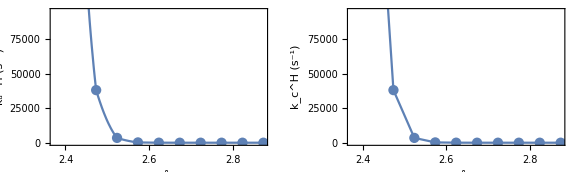

```mathematica
kHdiffplot[0,0,0]
```

{{2.37337,1.64279×10^6},{2.42337,634294.},{2.47337,227556.},{2.52337,105296.},{2.57337,66266.1},{2.62337,49643.4},{2.67337,42854.3},{2.72337,50180.5},{2.77337,317299.},{2.82337,171252.},{2.87337,93205.3}}

{{2.37337,1.64279×10^6},{2.42337,634294.},{2.47337,227556.},{2.52337,105296.},{2.57337,66266.1},{2.62337,49643.4},{2.67337,42854.3},{2.72337,50180.5},{2.77337,317299.},{2.82337,171252.},{2.87337,93205.3}}

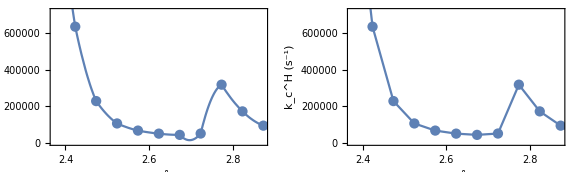

```mathematica
kHdiffplot[0,5,5]
```

## Functions for anodic (ka) and cathodic (kc) total rate constants - Deuterium

Anodic rate constant k_a(η):
(mumax and numax are the upper limits for the vibrational quantum numbers for the reactant and product vibrational states)

```mathematica
kaDEPTtotal[η_,mumax_,numax_,OptionsPattern[{Output->False}]]:=Module[
{output,kaD237,kaD242,kaD247,kaD252,kaD257,kaD262,kaD267,kaD272,kaD277,kaD282,kaD287,listkAD,kaDR,kaDtotal,kaD,kaDmax},

output=OptionValue[Output];

kaD237=AnodicRateConstantFGHBen[waveD237,Vel,η,λs,mumax,numax,T];
kaD242=AnodicRateConstantFGHBen[waveD242,Vel,η,λs,mumax,numax,T];
kaD247=AnodicRateConstantFGHBen[waveD247,Vel,η,λs,mumax,numax,T];
kaD252=AnodicRateConstantFGHBen[waveD252,Vel,η,λs,mumax,numax,T];
kaD257=AnodicRateConstantFGHBen[waveD257,Vel,η,λs,mumax,numax,T];
kaD262=AnodicRateConstantFGHBen[waveD262,Vel,η,λs,mumax,numax,T];
kaD267=AnodicRateConstantFGHBen[waveD267,Vel,η,λs,mumax,numax,T];
kaD272=AnodicRateConstantFGHBen[waveD272,Vel,η,λs,mumax,numax,T];
kaD277=AnodicRateConstantFGHBen[waveD277,Vel,η,λs,mumax,numax,T];
kaD282=AnodicRateConstantFGHBen[waveD282,Vel,η,λs,mumax,numax,T];
kaD287=AnodicRateConstantFGHBen[waveD287,Vel,η,λs,mumax,numax,T];

listkAD={{R237,kaD237},{R242,kaD242},{R247,kaD247},{R252,kaD252},{R257,kaD257},{R262,kaD262},{R267,kaD267},{R272,kaD272},{R277,kaD277},{R282,kaD282},{R287,kaD287}};

Off[InterpolatingFunction::dmval];
kaDR=Interpolation[listkAD,InterpolationOrder->2];

kaD[R_]:=If[kaDR[R]<0,0,kaDR[R]];

kaDmax=FindMaximum[kaD[x]Pav[x],{x,2.0,3.5}];
kaDtotal=NIntegrate[kaD[x]Pav[x],{x,0,∞}];

If[output,Print["k_a^D(total) = ",kaDtotal,"\nk_a^D(max) = ",kaDmax⟦1⟧," s^-1","\nR_a(max) = ",kaDmax⟦2,1,2⟧," Å"]];
kaDtotal
];
```

Cathodic rate constant k_c(η):
(mumax and numax are the upper limits for the vibrational quantum numbers for the reactant and product vibrational states)

```mathematica
kcDEPTtotal[η_,mumax_,numax_,OptionsPattern[{Output->False}]]:=Module[
{output,kcD237,kcD242,kcD247,kcD252,kcD257,kcD262,kcD267,kcD272,kcD277,kcD282,kcD287,listkCD,kcDR,kcDtotal,kcD,kcDmax},

output=OptionValue[Output];

kcD237=CathodicRateConstantFGHBen[waveD237,Vel,η,λs,mumax,numax,T];
kcD242=CathodicRateConstantFGHBen[waveD242,Vel,η,λs,mumax,numax,T];
kcD247=CathodicRateConstantFGHBen[waveD247,Vel,η,λs,mumax,numax,T];
kcD252=CathodicRateConstantFGHBen[waveD252,Vel,η,λs,mumax,numax,T];
kcD257=CathodicRateConstantFGHBen[waveD257,Vel,η,λs,mumax,numax,T];
kcD262=CathodicRateConstantFGHBen[waveD262,Vel,η,λs,mumax,numax,T];
kcD267=CathodicRateConstantFGHBen[waveD267,Vel,η,λs,mumax,numax,T];
kcD272=CathodicRateConstantFGHBen[waveD272,Vel,η,λs,mumax,numax,T];
kcD277=CathodicRateConstantFGHBen[waveD277,Vel,η,λs,mumax,numax,T];
kcD282=CathodicRateConstantFGHBen[waveD282,Vel,η,λs,mumax,numax,T];
kcD287=CathodicRateConstantFGHBen[waveD287,Vel,η,λs,mumax,numax,T];

listkCD={{R237,kcD237},{R242,kcD242},{R247,kcD247},{R252,kcD252},{R257,kcD257},{R262,kcD262},{R267,kcD267},{R272,kcD272},{R277,kcD277},{R282,kcD282},{R287,kcD287}};

Off[InterpolatingFunction::dmval];
kcDR=Interpolation[listkCD,InterpolationOrder->1];

kcD[R_]:=If[kcDR[R]<0,0,kcDR[R]];

kcDmax=FindMaximum[kcD[x]Pav[x],{x,2.0,3.5}];
kcDtotal=NIntegrate[kcD[x]Pav[x],{x,0,∞}];

If[output,Print["k_c^D(total) = ",kcDtotal,"\nk_c^D(max) = ",kcDmax⟦1⟧," s^-1","\nR_c(max) = ",kcDmax⟦2,1,2⟧," Å"]];
kcDtotal
];
```

Difference k_a-k_c:
(mumax and numax are the upper limits for the vibrational quantum numbers for the reactant and product vibrational states)

```mathematica
kDdiff[η_,mumax_,numax_]:=Module[
{kaD237,kaD242,kaD247,kaD252,kaD257,kaD262,kaD267,kaD272,kaD277,kaD282,kaD287,
kcD237,kcD242,kcD247,kcD252,kcD257,kcD262,kcD267,kcD272,kcD277,kcD282,kcD287,
listkAD,listkCD,kaDR,kcDR,kaDtotal,kcDtotal,kaD,kcD},

kaD237=AnodicRateConstantFGHBen[waveD237,Vel,η,λs,mumax,numax,T];
kaD242=AnodicRateConstantFGHBen[waveD242,Vel,η,λs,mumax,numax,T];
kaD247=AnodicRateConstantFGHBen[waveD247,Vel,η,λs,mumax,numax,T];
kaD252=AnodicRateConstantFGHBen[waveD252,Vel,η,λs,mumax,numax,T];
kaD257=AnodicRateConstantFGHBen[waveD257,Vel,η,λs,mumax,numax,T];
kaD262=AnodicRateConstantFGHBen[waveD262,Vel,η,λs,mumax,numax,T];
kaD267=AnodicRateConstantFGHBen[waveD267,Vel,η,λs,mumax,numax,T];
kaD272=AnodicRateConstantFGHBen[waveD272,Vel,η,λs,mumax,numax,T];
kaD277=AnodicRateConstantFGHBen[waveD277,Vel,η,λs,mumax,numax,T];
kaD282=AnodicRateConstantFGHBen[waveD282,Vel,η,λs,mumax,numax,T];
kaD287=AnodicRateConstantFGHBen[waveD287,Vel,η,λs,mumax,numax,T];

kcD237=CathodicRateConstantFGHBen[waveD237,Vel,η,λs,mumax,numax,T];
kcD242=CathodicRateConstantFGHBen[waveD242,Vel,η,λs,mumax,numax,T];
kcD247=CathodicRateConstantFGHBen[waveD247,Vel,η,λs,mumax,numax,T];
kcD252=CathodicRateConstantFGHBen[waveD252,Vel,η,λs,mumax,numax,T];
kcD257=CathodicRateConstantFGHBen[waveD257,Vel,η,λs,mumax,numax,T];
kcD262=CathodicRateConstantFGHBen[waveD262,Vel,η,λs,mumax,numax,T];
kcD267=CathodicRateConstantFGHBen[waveD267,Vel,η,λs,mumax,numax,T];
kcD272=CathodicRateConstantFGHBen[waveD272,Vel,η,λs,mumax,numax,T];
kcD277=CathodicRateConstantFGHBen[waveD277,Vel,η,λs,mumax,numax,T];
kcD282=CathodicRateConstantFGHBen[waveD282,Vel,η,λs,mumax,numax,T];
kcD287=CathodicRateConstantFGHBen[waveD287,Vel,η,λs,mumax,numax,T];

listkAD={{R237,kaD237},{R242,kaD242},{R247,kaD247},{R252,kaD252},{R257,kaD257},{R262,kaD262},{R267,kaD267},{R272,kaD272},{R277,kaD277},{R282,kaD282},{R287,kaD287}};
listkCD={{R237,kcD237},{R242,kcD242},{R247,kcD247},{R252,kcD252},{R257,kcD257},{R262,kcD262},{R267,kcD267},{R272,kcD272},{R277,kcD277},{R282,kcD282},{R287,kcD287}};

Off[InterpolatingFunction::dmval];
kaDR=Interpolation[listkAD,InterpolationOrder->2];
kcDR=Interpolation[listkCD,InterpolationOrder->1];

kaD[R_]:=If[kaDR[R]<0,0,kaDR[R]];
kcD[R_]:=If[kcDR[R]<0,0,kcDR[R]];

kaDtotal=NIntegrate[kaD[x]Pav[x],{x,0,∞}];
kcDtotal=NIntegrate[kcD[x]Pav[x],{x,0,∞}];
kaDtotal-kcDtotal
];
```

That seems to be the same function... Ignore.

```mathematica
kDdiffeta0[η_,mumax_,numax_]:=Module[
{kaD237,kaD242,kaD247,kaD252,kaD257,kaD262,kaD267,kaD272,kaD277,kaD282,kaD287,
kcD237,kcD242,kcD247,kcD252,kcD257,kcD262,kcD267,kcD272,kcD277,kcD282,kcD287,
listkAD,listkCD,kaDR,kcDR,kaDtotal,kcDtotal,kaD,kcD},

kaD237=AnodicRateConstantFGHBen[waveD237,Vel,η,λs,mumax,numax,T];
kaD242=AnodicRateConstantFGHBen[waveD242,Vel,η,λs,mumax,numax,T];
kaD247=AnodicRateConstantFGHBen[waveD247,Vel,η,λs,mumax,numax,T];
kaD252=AnodicRateConstantFGHBen[waveD252,Vel,η,λs,mumax,numax,T];
kaD257=AnodicRateConstantFGHBen[waveD257,Vel,η,λs,mumax,numax,T];
kaD262=AnodicRateConstantFGHBen[waveD262,Vel,η,λs,mumax,numax,T];
kaD267=AnodicRateConstantFGHBen[waveD267,Vel,η,λs,mumax,numax,T];
kaD272=AnodicRateConstantFGHBen[waveD272,Vel,η,λs,mumax,numax,T];
kaD277=AnodicRateConstantFGHBen[waveD277,Vel,η,λs,mumax,numax,T];
kaD282=AnodicRateConstantFGHBen[waveD282,Vel,η,λs,mumax,numax,T];
kaD287=AnodicRateConstantFGHBen[waveD287,Vel,η,λs,mumax,numax,T];

kcD237=CathodicRateConstantFGHBen[waveD237,Vel,η,λs,mumax,numax,T];
kcD242=CathodicRateConstantFGHBen[waveD242,Vel,η,λs,mumax,numax,T];
kcD247=CathodicRateConstantFGHBen[waveD247,Vel,η,λs,mumax,numax,T];
kcD252=CathodicRateConstantFGHBen[waveD252,Vel,η,λs,mumax,numax,T];
kcD257=CathodicRateConstantFGHBen[waveD257,Vel,η,λs,mumax,numax,T];
kcD262=CathodicRateConstantFGHBen[waveD262,Vel,η,λs,mumax,numax,T];
kcD267=CathodicRateConstantFGHBen[waveD267,Vel,η,λs,mumax,numax,T];
kcD272=CathodicRateConstantFGHBen[waveD272,Vel,η,λs,mumax,numax,T];
kcD277=CathodicRateConstantFGHBen[waveD277,Vel,η,λs,mumax,numax,T];
kcD282=CathodicRateConstantFGHBen[waveD282,Vel,η,λs,mumax,numax,T];
kcD287=CathodicRateConstantFGHBen[waveD287,Vel,η,λs,mumax,numax,T];

listkAD={{R237,kaD237},{R242,kaD242},{R247,kaD247},{R252,kaD252},{R257,kaD257},{R262,kaD262},{R267,kaD267},{R272,kaD272},{R277,kaD277},{R282,kaD282},{R287,kaD287}};
listkCD={{R237,kcD237},{R242,kcD242},{R247,kcD247},{R252,kcD252},{R257,kcD257},{R262,kcD262},{R267,kcD267},{R272,kcD272},{R277,kcD277},{R282,kcD282},{R287,kcD287}};

Off[InterpolatingFunction::dmval];
kaDR=Interpolation[listkAD,InterpolationOrder->2];
kcDR=Interpolation[listkCD,InterpolationOrder->1];

kaD[R_]:=If[kaDR[R]<0,0,kaDR[R]];
kcD[R_]:=If[kcDR[R]<0,0,kcDR[R]];

kaDtotal=NIntegrate[kaD[x]Pav[x],{x,0,∞}];
kcDtotal=NIntegrate[kcD[x]Pav[x],{x,0,∞}];
kaDtotal-kcDtotal
];
```

This function plots anodic and cathodic rate constants as functions of the DA distance:
η is overpotential;
mumax and numax are the upper limits for the vibrational quantum numbers for the reactant and product vibrational states

```mathematica
kDdiffplot[η_,mumax_,numax_]:=Module[
{kaD237,kaD242,kaD247,kaD252,kaD257,kaD262,kaD267,kaD272,kaD277,kaD282,kaD287,
kcD237,kcD242,kcD247,kcD252,kcD257,kcD262,kcD267,kcD272,kcD277,kcD282,kcD287,
listkAD,listkCD,kaDR,kcDR,kaDtotal,kcDtotal,kaD,kcD,kaDRplot,kcDRplot},

kaD237=AnodicRateConstantFGHBen[waveD237,Vel,η,λs,mumax,numax,T];
kaD242=AnodicRateConstantFGHBen[waveD242,Vel,η,λs,mumax,numax,T];
kaD247=AnodicRateConstantFGHBen[waveD247,Vel,η,λs,mumax,numax,T];
kaD252=AnodicRateConstantFGHBen[waveD252,Vel,η,λs,mumax,numax,T];
kaD257=AnodicRateConstantFGHBen[waveD257,Vel,η,λs,mumax,numax,T];
kaD262=AnodicRateConstantFGHBen[waveD262,Vel,η,λs,mumax,numax,T];
kaD267=AnodicRateConstantFGHBen[waveD267,Vel,η,λs,mumax,numax,T];
kaD272=AnodicRateConstantFGHBen[waveD272,Vel,η,λs,mumax,numax,T];
kaD277=AnodicRateConstantFGHBen[waveD277,Vel,η,λs,mumax,numax,T];
kaD282=AnodicRateConstantFGHBen[waveD282,Vel,η,λs,mumax,numax,T];
kaD287=AnodicRateConstantFGHBen[waveD287,Vel,η,λs,mumax,numax,T];

kcD237=CathodicRateConstantFGHBen[waveD237,Vel,η,λs,mumax,numax,T];
kcD242=CathodicRateConstantFGHBen[waveD242,Vel,η,λs,mumax,numax,T];
kcD247=CathodicRateConstantFGHBen[waveD247,Vel,η,λs,mumax,numax,T];
kcD252=CathodicRateConstantFGHBen[waveD252,Vel,η,λs,mumax,numax,T];
kcD257=CathodicRateConstantFGHBen[waveD257,Vel,η,λs,mumax,numax,T];
kcD262=CathodicRateConstantFGHBen[waveD262,Vel,η,λs,mumax,numax,T];
kcD267=CathodicRateConstantFGHBen[waveD267,Vel,η,λs,mumax,numax,T];
kcD272=CathodicRateConstantFGHBen[waveD272,Vel,η,λs,mumax,numax,T];
kcD277=CathodicRateConstantFGHBen[waveD277,Vel,η,λs,mumax,numax,T];
kcD282=CathodicRateConstantFGHBen[waveD282,Vel,η,λs,mumax,numax,T];
kcD287=CathodicRateConstantFGHBen[waveD287,Vel,η,λs,mumax,numax,T];

listkAD={{R237,kaD237},{R242,kaD242},{R247,kaD247},{R252,kaD252},{R257,kaD257},{R262,kaD262},{R267,kaD267},{R272,kaD272},{R277,kaD277},{R282,kaD282},{R287,kaD287}};
Print[listkAD];
listkCD={{R237,kcD237},{R242,kcD242},{R247,kcD247},{R252,kcD252},{R257,kcD257},{R262,kcD262},{R267,kcD267},{R272,kcD272},{R277,kcD277},{R282,kcD282},{R287,kcD287}};
Print[listkCD];

Off[InterpolatingFunction::dmval];
kaDR=Interpolation[listkAD,InterpolationOrder->2];
kcDR=Interpolation[listkCD,InterpolationOrder->1];

kaD[R_]:=If[kaDR[R]<0,0,kaDR[R]];
kcD[R_]:=If[kcDR[R]<0,0,kcDR[R]];

kaDRplot=Plot[kaD[x],{x,2,4},ImageSize->Large];
kcDRplot=Plot[kcD[x],{x,2,4},ImageSize->Large];

GraphicsRow[
{Show[ListPlot[listkAD,ImageSize->Large],kaDRplot,Axes->False,Frame->True,FrameLabel->{"R, Å","k_a^D (s^-1)"}],
Show[ListPlot[listkCD,ImageSize->Large],kcDRplot,Axes->False,Frame->True,FrameLabel->{"R, Å","k_c^D (s^-1)"}]},
ImageSize->Large
]
];
```

Let’s see:

{{2.37337,152271.},{2.42337,14278.8},{2.47337,687.281},{2.52337,18.9205},{2.57337,0.322951},{2.62337,0.0146308},{2.67337,0.0000267116},{2.72337,1.28219×10^-7},{2.77337,9.31445×10^-10},{2.82337,1.31261×10^-12},{2.87337,1.00317×10^-10}}

{{2.37337,152271.},{2.42337,14278.8},{2.47337,687.281},{2.52337,18.9205},{2.57337,0.322951},{2.62337,0.0146308},{2.67337,0.0000267116},{2.72337,1.28219×10^-7},{2.77337,9.31445×10^-10},{2.82337,1.31261×10^-12},{2.87337,1.00317×10^-10}}

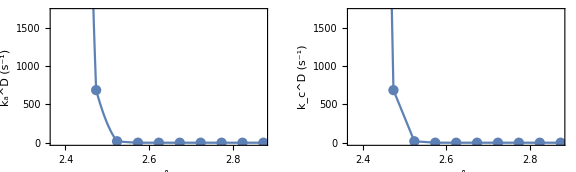

```mathematica
kDdiffplot[0,0,0]
```

{{2.37337,742637.},{2.42337,267286.},{2.47337,111757.},{2.52337,62043.7},{2.57337,41884.6},{2.62337,31660.9},{2.67337,27227.1},{2.72337,31601.5},{2.77337,207406.},{2.82337,107964.},{2.87337,55959.6}}

{{2.37337,742637.},{2.42337,267286.},{2.47337,111757.},{2.52337,62043.7},{2.57337,41884.6},{2.62337,31660.9},{2.67337,27227.1},{2.72337,31601.5},{2.77337,207406.},{2.82337,107964.},{2.87337,55959.6}}

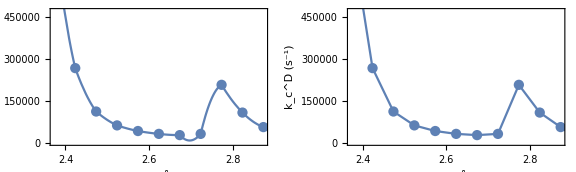

```mathematica
kDdiffplot[0,5,5]
```

## R_max: maximizes product of k(R)P(R)

Standard rate constant and the dominant donor-acceptor distance for anodic process - distance at which the rate constant reaches its maximum value:

```mathematica
η0=0.0;
```

```mathematica
ksH=kaHEPTtotal[η0,6,6,Output->True]
```

k_a^H(total) = 114009.
k_a^H(max) = 436181. s^-1
R_a(max) = 2.45753 Å

114009.

```mathematica
ksD=kaDEPTtotal[η0,6,6,Output->True]
```

k_a^D(total) = 61965.5
k_a^D(max) = 242946. s^-1
R_a(max) = 2.53653 Å

61965.5

```mathematica
KIE=ksH/ksD
```

1.83987

Standard rate constant and the dominant donor-acceptor distance for cathodic process - distance at which the rate constant reaches its maximum value:

```mathematica
ksH=kcHEPTtotal[η0,6,6,Output->True]
```

k_c^H(total) = 118130.
k_c^H(max) = 477800. s^-1
R_c(max) = 2.45599 Å

118130.

```mathematica
ksD=kcDEPTtotal[η0,6,6,Output->True]
```

k_c^D(total) = 63886.
k_c^D(max) = 249302. s^-1
R_c(max) = 2.50849 Å

63886.

```mathematica
KIE=ksH/ksD
```

1.84908

## Analysis of main contributions to standard rate constant at R≈R(max)

```mathematica
TableAnodicRateConstantFGHBen[waveH247,Vel,η0,λs,6,6,T]
```

kT Log[Z_2/Z_1]=-0.0004034 kcal/mol; λ=21.4 kcal/mol; η=0. V; k_a(total)=227556. s^-1 |  |  |  |  |  |  |  | 
μ | ν | P_μ | S | ΔU_μν | ΔG(η) | exp[-βΔG(η)] | k_μν(η) | %
0 | 0 | 9.98872e-1 | 3.48321e-3 |    0.000 |    5.350 | 1.19838e-4 | 3.82075e4 |    16.771
0 | 1 | 9.98872e-1 | 9.78237e-2 |    4.582 |    7.886 | 1.65699e-6 | 1.55323e4 |     6.818
0 | 2 | 9.98872e-1 | 6.6992e-1 |    6.815 |    9.300 | 1.52548e-7 | 1.03649e4 |     4.550
0 | 3 | 9.98872e-1 | 1.85866e-1 |    9.386 |   11.072 | 7.65856e-9 | 1.58956e2 |     0.070
0 | 4 | 9.98872e-1 | 3.72649e-2 |   12.770 |   13.640 | 1.00494e-10 | 5.02735e-1 |     0.000
0 | 5 | 9.98872e-1 | 5.12059e-3 |   16.524 |   16.802 | 4.83398e-13 | 4.48247e-4 |     1.968×10^-7
0 | 6 | 9.98872e-1 | 4.89393e-4 |   20.627 |   20.634 | 7.50859e-16 | 1.07992e-7 |     4.740×10^-11
1 | 0 | 1.06995e-3 | 5.36646e-1 |   -4.052 |    3.516 | 2.64875e-3 | 1.34844e8 |    63.402
1 | 1 | 1.06995e-3 | 2.63341e-1 |    0.530 |    5.618 | 7.61682e-5 | 1.83709e6 |     0.864
1 | 2 | 1.06995e-3 | 4.75606e-5 |    2.763 |    6.820 | 1.00176e-5 | 4.4337e1 |     0.000
1 | 3 | 1.06995e-3 | 1.26836e-1 |    5.334 |    8.349 | 7.58516e-7 | 9.37219e3 |     0.004
1 | 4 | 1.06995e-3 | 5.94942e-2 |    8.718 |   10.596 | 1.70909e-8 | 1.10369e2 |     0.000
1 | 5 | 1.06995e-3 | 1.19095e-2 |   12.472 |   13.403 | 1.49788e-10 | 2.34945e-1 |     1.105×10^-7
1 | 6 | 1.06995e-3 | 1.5737e-3 |   16.575 |   16.847 | 4.48163e-13 | 1.28339e-4 |     6.034×10^-11
2 | 0 | 5.77458e-5 | 3.62e-1 |   -5.782 |    2.850 | 8.15269e-3 | 2.90711e8 |     7.377
2 | 1 | 5.77458e-5 | 7.81024e-2 |   -1.199 |    4.767 | 3.20464e-4 | 2.2981e6 |     0.058
2 | 2 | 5.77458e-5 | 8.46317e-2 |    1.033 |    5.879 | 4.90782e-5 | 3.81064e5 |     0.010
2 | 3 | 5.77458e-5 | 1.68211e-1 |    3.605 |    7.304 | 4.42864e-6 | 7.01391e4 |     0.002
2 | 4 | 5.77458e-5 | 2.27742e-1 |    6.988 |    9.414 | 1.2569e-7 | 2.919e3 |     0.000
2 | 5 | 5.77458e-5 | 6.75494e-2 |   10.743 |   12.069 | 1.42309e-9 | 1.14597e1 |     2.908×10^-7
2 | 6 | 5.77458e-5 | 1.05752e-2 |   14.845 |   15.347 | 5.63275e-12 | 9.30289e-3 |     2.361×10^-10
3 | 0 | 2.90556e-7 | 8.7781e-2 |   -8.917 |    1.820 | 4.63204e-2 | 4.44997e8 |     0.057
3 | 1 | 2.90556e-7 | 3.92313e-1 |   -4.335 |    3.402 | 3.20866e-3 | 1.20038e8 |     0.015
3 | 2 | 2.90556e-7 | 7.68422e-2 |   -2.103 |    4.350 | 6.47583e-4 | 4.59862e6 |     0.001
3 | 3 | 2.90556e-7 | 2.55969e-2 |    0.469 |    5.587 | 8.03103e-5 | 1.88252e5 |     0.000
3 | 4 | 2.90556e-7 | 1.78099e-1 |    3.853 |    7.450 | 3.46333e-6 | 5.83111e4 |     7.445×10^-6
3 | 5 | 2.90556e-7 | 1.82823e-1 |    7.607 |    9.829 | 6.2379e-8 | 1.18712e3 |     1.516×10^-7
3 | 6 | 2.90556e-7 | 4.89271e-2 |   11.710 |   12.806 | 4.10042e-10 | 2.5227e |     3.221×10^-10
4 | 0 | 7.56211e-10 | 9.70912e-3 |  -12.443 |    0.937 | 2.05633e-1 | 2.62474e8 |     0.000
4 | 1 | 7.56211e-10 | 1.48243e-1 |   -7.861 |    2.141 | 2.69382e-2 | 4.19452e8 |     0.000
4 | 2 | 7.56211e-10 | 1.33634e-1 |   -5.629 |    2.906 | 7.41541e-3 | 9.72326e7 |     0.000
4 | 3 | 7.56211e-10 | 2.56186e-1 |   -3.057 |    3.931 | 1.31494e-3 | 3.14661e7 |     0.000
4 | 4 | 7.56211e-10 | 3.03636e-3 |    0.327 |    5.514 | 9.07725e-5 | 2.52338e4 |     8.386×10^-9
4 | 5 | 7.56211e-10 | 2.21567e-1 |    4.081 |    7.585 | 2.75566e-6 | 5.79499e4 |     1.926×10^-8
4 | 6 | 7.56211e-10 | 1.77547e-1 |    8.184 |   10.224 | 3.20452e-8 | 6.0477e2 |     2.010×10^-10
5 | 0 | 9.71882e-13 | 3.80316e-4 |  -16.387 |    0.293 | 6.09351e-1 | 4.14263e7 |     1.769×10^-8
5 | 1 | 9.71882e-13 | 1.93756e-2 |  -11.805 |    1.075 | 1.62809e-1 | 3.98892e8 |     1.704×10^-7
5 | 2 | 9.71882e-13 | 3.23147e-2 |   -9.573 |    1.634 | 6.34194e-2 | 2.30779e8 |     9.856×10^-8
5 | 3 | 9.71882e-13 | 2.03089e-1 |   -7.001 |    2.422 | 1.67765e-2 | 3.4759e8 |     1.485×10^-7
5 | 4 | 9.71882e-13 | 2.93294e-1 |   -3.617 |    3.694 | 1.9602e-3 | 5.41419e7 |     2.312×10^-8
5 | 5 | 9.71882e-13 | 5.74605e-4 |    0.137 |    5.419 | 1.06704e-4 | 5.61234e3 |     2.397×10^-12
5 | 6 | 9.71882e-13 | 2.38542e-1 |    4.240 |    7.680 | 2.34877e-6 | 5.33315e4 |     2.278×10^-11
6 | 0 | 7.19802e-16 | 2.40195e-7 |  -20.658 |    0.006 | 9.89213e-1 | 7.01481e4 |     2.219×10^-14
6 | 1 | 7.19802e-16 | 7.99262e-4 |  -16.075 |    0.331 | 5.7183e-1 | 7.93642e7 |     2.510×10^-11
6 | 2 | 7.19802e-16 | 2.57065e-3 |  -13.843 |    0.667 | 3.24391e-1 | 1.20577e8 |     3.814×10^-11
6 | 3 | 7.19802e-16 | 3.27578e-2 |  -11.272 |    1.198 | 1.32324e-1 | 5.31678e8 |     1.682×10^-10
6 | 4 | 7.19802e-16 | 1.78314e-1 |   -7.888 |    2.133 | 2.73347e-2 | 5.12475e8 |     1.621×10^-10
6 | 5 | 7.19802e-16 | 3.30375e-1 |   -4.134 |    3.483 | 2.80029e-3 | 8.78915e7 |     2.780×10^-11
6 | 6 | 7.19802e-16 | 6.43131e-3 |   -0.031 |    5.334 | 1.23006e-4 | 7.24105e4 |     2.290×10^-14

```mathematica
TableAnodicRateConstantFGHBen[waveD252,Vel,η0,λs,6,6,T]
```

kT Log[Z_2/Z_1]=0.0007089 kcal/mol; λ=21.4 kcal/mol; η=0. V; k_a(total)=62044.1 s^-1 |  |  |  |  |  |  |  | 
μ | ν | P_μ | S | ΔU_μν | ΔG(η) | exp[-βΔG(η)] | k_μν(η) | %
0 | 0 | 9.99372e-1 | 1.72761e-6 |    0.000 |    5.350 | 1.19725e-4 | 1.89324e1 |     0.030
0 | 1 | 9.99372e-1 | 8.48185e-5 |    3.739 |    7.383 | 3.87444e-6 | 3.10084e1 |     0.050
0 | 2 | 9.99372e-1 | 2.13175e-2 |    6.998 |    9.422 | 1.24153e-7 | 2.69981e2 |     0.435
0 | 3 | 9.99372e-1 | 7.96472e-1 |    8.044 |   10.128 | 3.76558e-8 | 3.17148e3 |     5.108
0 | 4 | 9.99372e-1 | 1.07906e-1 |    9.687 |   11.290 | 5.2983e-9 | 6.47195e1 |     0.104
0 | 5 | 9.99372e-1 | 5.79553e-2 |   11.536 |   12.673 | 5.13718e-10 | 3.70656e |     0.006
0 | 6 | 9.99372e-1 | 1.35409e-2 |   13.663 |   14.363 | 2.96468e-11 | 5.72952e-2 |     0.000
1 | 0 | 5.16134e-4 | 5.78896e-3 |   -4.484 |    3.343 | 3.5443e-3 | 1.96222e6 |     1.632
1 | 1 | 5.16134e-4 | 9.42508e-3 |   -0.746 |    4.984 | 2.22167e-4 | 1.91894e5 |     0.160
1 | 2 | 5.16134e-4 | 6.46637e-2 |    2.514 |    6.681 | 1.26689e-5 | 7.60191e4 |     0.063
1 | 3 | 5.16134e-4 | 1.16908e-1 |    3.560 |    7.278 | 4.62327e-6 | 5.08547e4 |     0.042
1 | 4 | 5.16134e-4 | 1.56471e-1 |    5.203 |    8.268 | 8.69842e-7 | 1.32186e4 |     0.011
1 | 5 | 5.16134e-4 | 3.76217e-1 |    7.051 |    9.457 | 1.16946e-7 | 4.49579e3 |     0.004
1 | 6 | 5.16134e-4 | 1.9546e-1 |    9.179 |   10.924 | 9.83148e-9 | 2.1266e2 |     0.000
2 | 0 | 1.07405e-4 | 8.15374e-1 |   -5.414 |    2.986 | 6.48002e-3 | 5.15696e8 |    89.273
2 | 1 | 1.07405e-4 | 1.40163e-1 |   -1.676 |    4.545 | 4.65884e-4 | 6.0134e6 |     1.041
2 | 2 | 1.07405e-4 | 1.76762e-2 |    1.584 |    6.172 | 2.994e-5 | 4.87049e4 |     0.008
2 | 3 | 1.07405e-4 | 4.45916e-3 |    2.630 |    6.746 | 1.13533e-5 | 4.70396e3 |     0.001
2 | 4 | 1.07405e-4 | 4.4777e-5 |    4.273 |    7.700 | 2.26875e-6 | 9.67611e |     1.675×10^-6
2 | 5 | 1.07405e-4 | 9.68912e-3 |    6.121 |    8.849 | 3.26421e-7 | 3.14372e2 |     0.000
2 | 6 | 1.07405e-4 | 8.55511e-3 |    8.249 |   10.270 | 2.96684e-8 | 2.70472e1 |     4.682×10^-6
3 | 0 | 4.24434e-6 | 1.05256e-1 |   -7.329 |    2.313 | 2.01519e-2 | 2.18704e8 |     1.496
3 | 1 | 4.24434e-6 | 1.66134e-1 |   -3.590 |    3.706 | 1.92128e-3 | 3.00459e7 |     0.206
3 | 2 | 4.24434e-6 | 2.92436e-1 |   -0.331 |    5.186 | 1.57915e-4 | 4.22798e6 |     0.029
3 | 3 | 4.24434e-6 | 8.66378e-4 |    0.715 |    5.714 | 6.48025e-5 | 5.14464e3 |     0.000
3 | 4 | 4.24434e-6 | 1.68147e-1 |    2.359 |    6.595 | 1.46597e-5 | 2.28362e5 |     0.002
3 | 5 | 4.24434e-6 | 5.89548e-3 |    4.207 |    7.661 | 2.42503e-6 | 1.36007e3 |     9.304×10^-6
3 | 6 | 4.24434e-6 | 1.27852e-1 |    6.334 |    8.986 | 2.5881e-7 | 3.3087e3 |     0.000
4 | 0 | 3.62475e-7 | 6.20848e-2 |   -8.786 |    1.859 | 4.33947e-2 | 2.9325e8 |     0.171
4 | 1 | 3.62475e-7 | 3.97682e-1 |   -5.048 |    3.124 | 5.12923e-3 | 1.97403e8 |     0.115
4 | 2 | 3.62475e-7 | 1.35626e-2 |   -1.788 |    4.494 | 5.08461e-4 | 6.3559e5 |     0.000
4 | 3 | 3.62475e-7 | 2.25016e-2 |   -0.742 |    4.986 | 2.21585e-4 | 4.56925e5 |     0.000
4 | 4 | 3.62475e-7 | 1.1889e-1 |    0.901 |    5.810 | 5.50926e-5 | 6.00588e5 |     0.000
4 | 5 | 3.62475e-7 | 5.07391e-2 |    2.749 |    6.813 | 1.01353e-5 | 4.78489e4 |     0.000
4 | 6 | 3.62475e-7 | 7.00524e-2 |    4.877 |    8.067 | 1.22239e-6 | 8.25621e3 |     4.823×10^-6
5 | 0 | 1.04745e-8 | 1.04804e-2 |  -10.886 |    1.292 | 1.1306e-1 | 1.42323e8 |     0.002
5 | 1 | 1.04745e-8 | 2.20121e-1 |   -7.147 |    2.373 | 1.82126e-2 | 4.10904e8 |     0.007
5 | 2 | 1.04745e-8 | 2.10737e-1 |   -3.888 |    3.583 | 2.36477e-3 | 4.71394e7 |     0.001
5 | 3 | 1.04745e-8 | 5.46425e-3 |   -2.842 |    4.024 | 1.1238e-3 | 5.71999e5 |     9.657×10^-6
5 | 4 | 1.04745e-8 | 5.35511e-2 |   -1.199 |    4.768 | 3.20132e-4 | 1.57406e6 |     0.000
5 | 5 | 1.04745e-8 | 1.35499e-1 |    0.649 |    5.680 | 6.86347e-5 | 8.52022e5 |     0.000
5 | 6 | 1.04745e-8 | 1.60359e-2 |    2.777 |    6.829 | 9.87238e-6 | 1.47351e4 |     2.488×10^-7
6 | 0 | 2.18807e-10 | 9.85015e-4 |  -13.178 |    0.790 | 2.63669e-1 | 3.58283e7 |     0.000
6 | 1 | 2.18807e-10 | 5.86429e-2 |   -9.440 |    1.671 | 5.95501e-2 | 3.90886e8 |     0.000
6 | 2 | 2.18807e-10 | 2.67587e-1 |   -6.180 |    2.706 | 1.0381e-2 | 2.76551e8 |     0.000
6 | 3 | 2.18807e-10 | 3.12496e-2 |   -5.134 |    3.091 | 5.42251e-3 | 1.64308e7 |     5.795×10^-6
6 | 4 | 2.18807e-10 | 1.01004e-1 |   -3.491 |    3.747 | 1.79201e-3 | 1.70117e7 |     5.999×10^-6
6 | 5 | 2.18807e-10 | 7.09827e-3 |   -1.643 |    4.561 | 4.54062e-4 | 2.96739e5 |     1.046×10^-7
6 | 6 | 2.18807e-10 | 1.63435e-1 |    0.485 |    5.595 | 7.9159e-5 | 1.18479e6 |     4.178×10^-7

## Rate Convergence

```mathematica
KIEData=Table[{η,Log[10,kaHEPTtotal[η,m,5,Output->False]/kaDEPTtotal[η,m,5,Output->False]]},{η,η0-0.5,η0,0.05},{m,1,5}]
```

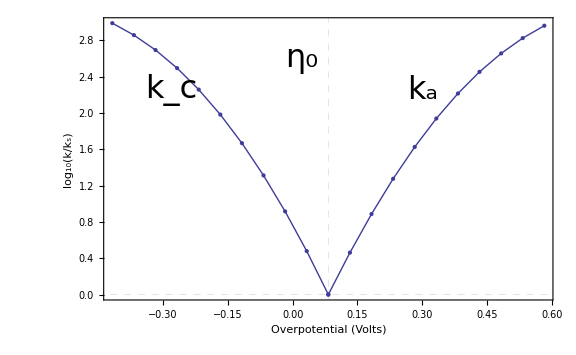

```mathematica
ListLinePlot[KIEData,
Mesh->All,
ImageSize->Large,
Axes->False,
Frame->True,
FrameLabel->{{Style["KIE",24,FontFamily->"Helvetica"],},{"Number of States",Style["Proton k_s = "<>ToString[ScientificForm[ks],FormatType->StandardForm]<>" sec^-1",32,FontFamily->"Helvetica"]}},
BaseStyle->{FontFamily->"Helvetica",FontSize->24}
]
```

## Plots of the overlaps

obtained after finding main contributions to anodic and cathodic rate constants at dominant donor-acceptor distance

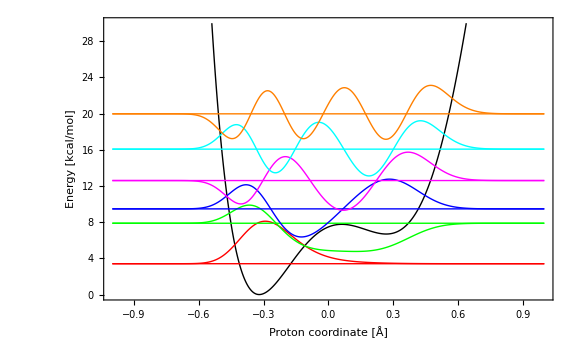

```mathematica
wavelist=waveH247;
ListLinePlot[{Table[{wavelist[[1,2]][[i,1]],wavelist[[1,2]][[i,2]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[1]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[1]]+50*wavelist[[1,3,1]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[2]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[2]]+50*wavelist[[1,3,2]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[3]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[3]]+50*wavelist[[1,3,3]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[4]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[4]]+50*wavelist[[1,3,4]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[5]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[5]]+50*wavelist[[1,3,5]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[6]]},{i,1,Length[wavelist[[1,3,1]]]}],Table[{wavelist[[1,2]][[i,1]],wavelist[[1,1]][[6]]+50*wavelist[[1,3,6]][[i]]},{i,1,Length[wavelist[[1,3,1]]]}]},PlotRange->{0,30},ImageSize->Large,BaseStyle->{FontSize->16},Axes->False,Frame->True,FrameLabel->{"Proton coordinate [Å]","Energy [kcal/mol]"},PlotStyle->{{Black,Thick},Red,Red,Green,Green,Blue,Blue,Magenta,Magenta,Cyan,Cyan,Orange,Orange}]
```

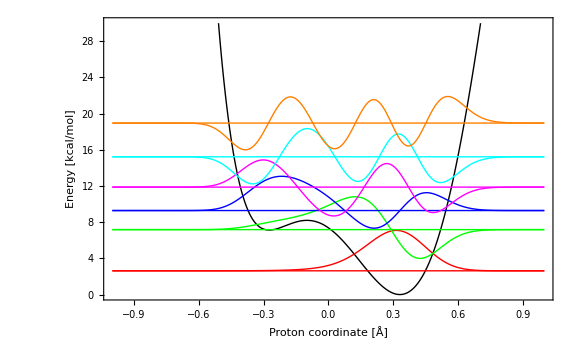

```mathematica
wavelist=waveH247;
ListLinePlot[{Table[{wavelist[[2,2]][[i,1]],wavelist[[2,2]][[i,2]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[1]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[1]]+50*wavelist[[2,3,1]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[2]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[2]]+50*wavelist[[2,3,2]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[3]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[3]]+50*wavelist[[2,3,3]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[4]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[4]]+50*wavelist[[2,3,4]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[5]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[5]]+50*wavelist[[2,3,5]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[6]]},{i,1,Length[wavelist[[2,3,1]]]}],Table[{wavelist[[2,2]][[i,1]],wavelist[[2,1]][[6]]+50*wavelist[[2,3,6]][[i]]},{i,1,Length[wavelist[[2,3,1]]]}]},PlotRange->{0,30},ImageSize->Large,BaseStyle->{FontSize->16},Axes->False,Frame->True,FrameLabel->{"Proton coordinate [Å]","Energy [kcal/mol]"},PlotStyle->{{Black,Thick},Red,Red,Green,Green,Blue,Blue,Magenta,Magenta,Cyan,Cyan,Orange,Orange}]
```

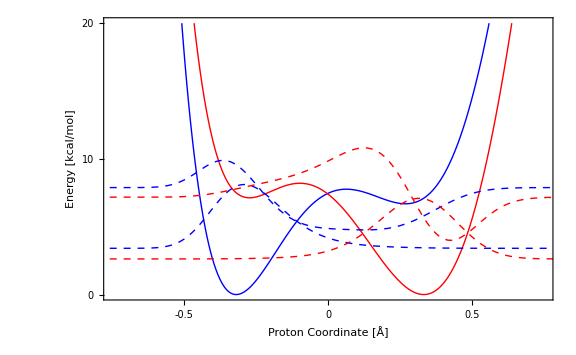

```mathematica
wavelist1=waveH247;
ListLinePlot[{
Table[{wavelist1⟦1,2⟧⟦i,1⟧,wavelist1⟦1,2⟧⟦i,2⟧},{i,1,Length[wavelist1⟦1,3,1⟧]}],Table[{wavelist1⟦2,2⟧⟦i,1⟧,wavelist1⟦2,2⟧⟦i,2⟧},{i,1,Length[wavelist1⟦2,3,1⟧]}],
Table[{wavelist1⟦1,2⟧⟦i,1⟧,wavelist1⟦1,1⟧⟦1⟧+50*wavelist1⟦1,3,1⟧⟦i⟧},{i,1,Length[wavelist1⟦1,3,1⟧]}],
Table[{wavelist1⟦1,2⟧⟦i,1⟧,wavelist1⟦1,1⟧⟦2⟧+50*wavelist1⟦1,3,2⟧⟦i⟧},{i,1,Length[wavelist1⟦1,3,2⟧]}],
Table[{wavelist1⟦2,2⟧⟦i,1⟧,wavelist1⟦2,1⟧⟦1⟧+50*wavelist1⟦2,3,1⟧⟦i⟧},{i,1,Length[wavelist1⟦2,3,1⟧]}],
Table[{wavelist1⟦2,2⟧⟦i,1⟧,wavelist1⟦2,1⟧⟦2⟧+50*wavelist1⟦2,3,2⟧⟦i⟧},{i,1,Length[wavelist1⟦2,3,2⟧]}]
},
PlotRange->{{-0.75,0.75},{0,20}},
FrameTicks->{{{0,10,20,30},None},{{-0.50,0,0.50},None}},
ImageSize->Large,
BaseStyle->{FontFamily->"Helvetica",FontSize->16},
Axes->False,
Frame->True,
FrameLabel->{"Proton Coordinate [Å]","Energy [kcal/mol]"},
PlotStyle->{{Blue,Thick},{Red,Thick},{Blue,Dashed},{Blue,Dashed},{Red,Dashed},{Red,Dashed}}
]
```

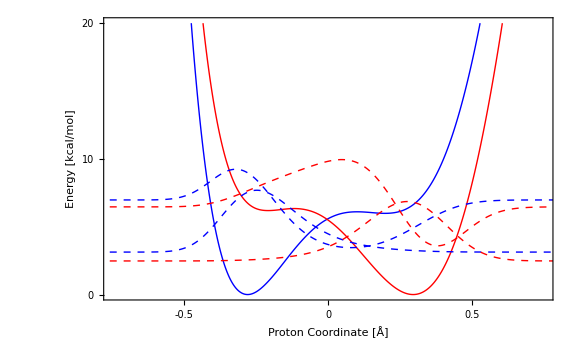

```mathematica
wavelist1=waveH242;
ListLinePlot[{
Table[{wavelist1⟦1,2⟧⟦i,1⟧,wavelist1⟦1,2⟧⟦i,2⟧},{i,1,Length[wavelist1⟦1,3,1⟧]}],Table[{wavelist1⟦2,2⟧⟦i,1⟧,wavelist1⟦2,2⟧⟦i,2⟧},{i,1,Length[wavelist1⟦2,3,1⟧]}],
Table[{wavelist1⟦1,2⟧⟦i,1⟧,wavelist1⟦1,1⟧⟦1⟧+50*wavelist1⟦1,3,1⟧⟦i⟧},{i,1,Length[wavelist1⟦1,3,1⟧]}],
Table[{wavelist1⟦1,2⟧⟦i,1⟧,wavelist1⟦1,1⟧⟦2⟧+50*wavelist1⟦1,3,2⟧⟦i⟧},{i,1,Length[wavelist1⟦1,3,2⟧]}],
Table[{wavelist1⟦2,2⟧⟦i,1⟧,wavelist1⟦2,1⟧⟦1⟧+50*wavelist1⟦2,3,1⟧⟦i⟧},{i,1,Length[wavelist1⟦2,3,1⟧]}],
Table[{wavelist1⟦2,2⟧⟦i,1⟧,wavelist1⟦2,1⟧⟦2⟧+50*wavelist1⟦2,3,2⟧⟦i⟧},{i,1,Length[wavelist1⟦2,3,2⟧]}]
},
PlotRange->{{-0.75,0.75},{0,20}},
FrameTicks->{{{0,10,20,30},None},{{-0.50,0,0.50},None}},
ImageSize->Large,
BaseStyle->{FontFamily->"Helvetica",FontSize->16},
Axes->False,
Frame->True,
FrameLabel->{"Proton Coordinate [Å]","Energy [kcal/mol]"},
PlotStyle->{{Blue,Thick},{Red,Thick},{Blue,Dashed},{Blue,Dashed},{Red,Dashed},{Red,Dashed}}
]
```